## Basics

```mathematica
dim=3;
d=2;
variables=Table[Subscript[ξ, j],{j,1,dim}];
```

### Noncommutative Multiply for Matrices

```mathematica
Unprotect[NonCommutativeMultiply];
NonCommutativeMultiply[m1__List,m2__List]:=Inner[NonCommutativeMultiply,m1,m2,Plus];
NonCommutativeMultiply[m1__List,m2_]:= Map[NonCommutativeMultiply[#1,m2]&,m1];
NonCommutativeMultiply[m1_,m2__List]:= Map[NonCommutativeMultiply[m1,#1]&,m2];
Protect[NonCommutativeMultiply];
```

### Derivations on T_θ

```mathematica
δ[a_,list_]:=If[list[[1]]≠ 0,δ[Subscript[δ, 1][a],list-{1,0,0}],If[list[[2]]≠0,δ[Subscript[δ, 2][a],list-{0,1,0}],If[list[[3]]≠0,δ[Subscript[δ, 3][a],list-{0,0,1}],a]]]

Subscript[δ, j_][x__+y_]:= Subscript[δ, j][x]+Subscript[δ, j][y]
Subscript[δ, j_][x_^n_. *k_]/;Or[MemberQ[variables,x],,MemberQ[{τ1^2,τ1,τ2^2,τ2,abs[τ]},x],Element[x,Integers],Element[x,Complexes],Element[x,Reals]]:=x^n*Subscript[δ, j][k]
(*Subscript[δ, j_][a_^*]:=-(Subscript[δ, j][a])^*;*)
SuperStar[Subscript[δ, j_][a_]]:=-Subscript[δ, j][SuperStar[a]];
Subscript[δ, j_][I]:=0;
Subscript[δ, j_][0]:=0;
Subscript[δ, j_][x__**y_]:= Subscript[δ, j][x]**y+x**Subscript[δ, j][y];
Subscript[δ, j_][list__List]:=Map[Subscript[δ, j],list];
```

### Noncommutative Multiply

```mathematica
NCM={(x_+y_)**z_->(x**z)+(y**z),
x_**(y_+z_)->( x**y)+(x**z),
x_**(y_^n_.*z_)/;Or[MemberQ[variables,y],Element[y,Integers],Element[y,Complexes],Element[x,Reals]]->y^n* (x**z),(y_^n_.*z_)**x_/;Or[MemberQ[variables,y],Element[y,Integers],Element[y,Complexes],Element[x,Reals]]->y^n* (z**x),
x_**0-> 0,
0**x_-> 0,
x_**1->x,
1**x_->x, 
k^(n_.)**k^(m_.)-> k^(n+m)};
```

### Derivatives of b_0

```mathematica
Der:={
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],Subscript[ξ, 1]]-> - 2 Subscript[ξ, 1] k^4**Subscript[b, 0]^2,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],Subscript[ξ, 2]]-> - 2 Subscript[ξ, 2] k^4**Subscript[b, 0]^2,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],Subscript[ξ, 3]]->  -2 Subscript[ξ, 3] k^4**Subscript[b, 0]^2,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 1],2}]->  -2 k^4**Subscript[b, 0]^2+8 Subscript[ξ, 1]^2 k^8**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 2],2}]->  -2 k^4**Subscript[b, 0]^2+8 Subscript[ξ, 2]^2 k^8**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 3],2}]-> - 2 k^4**Subscript[b, 0]^2+8 Subscript[ξ, 3]^2 k^8**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 1],1},{Subscript[ξ, 2],1}]->  8 Subscript[ξ, 1] Subscript[ξ, 2] k^8**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 1],1},{Subscript[ξ, 3],1}]->  8 Subscript[ξ, 1] Subscript[ξ, 3] k^8**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 2],1},{Subscript[ξ, 3],1}]->  8 Subscript[ξ, 2] Subscript[ξ, 3] k^8**Subscript[b, 0]^3};
```

## Symbol of the Laplacian and b_2

### Symbol of the Laplacian on Functions

```mathematica
Subscript[a, 2]={{k^4 Subscript[ξ, 1]^2+k^4 Subscript[ξ, 2]^2+k^4 Subscript[ξ, 3]^2,0,0},{0,k^4 Subscript[ξ, 1]^2+k^4 Subscript[ξ, 2]^2+k^4 Subscript[ξ, 3]^2,0},{0,0,k^4 Subscript[ξ, 1]^2+k^4 Subscript[ξ, 2]^2+k^4 Subscript[ξ, 3]^2}};
Subscript[a, 1]={{(2 k^3**Subscript[δ, 1][k]+(1/k)**Subscript[δ, 1][k^6]**(1/k)+2 k^5**Subscript[δ, 1][1/k^2]**k) Subscript[ξ, 1]+(2 k^3**Subscript[δ, 2][k]+k**Subscript[δ, 2][k^2]**k) Subscript[ξ, 2]+(2 k^3**Subscript[δ, 3][k]+k**Subscript[δ, 3][k^2]**k) Subscript[ξ, 3],(-k**Subscript[δ, 2][k^2]**k+k^5**Subscript[δ, 2][1/k^2]**k) Subscript[ξ, 1]+((1/k)**Subscript[δ, 1][k^6]**(1/k)+k^5**Subscript[δ, 1][1/k^2]**k) Subscript[ξ, 2],(-k**Subscript[δ, 3][k^2]**k+k^5**Subscript[δ, 3][1/k^2]**k) Subscript[ξ, 1]+((1/k)**Subscript[δ, 1][k^6]**(1/k)+k^5**Subscript[δ, 1][1/k^2]**k) Subscript[ξ, 3]},{((1/k)**Subscript[δ, 2][k^6]**(1/k)+k^5**Subscript[δ, 2][1/k^2]**k) Subscript[ξ, 1]+(-k**Subscript[δ, 1][k^2]**k+k^5**Subscript[δ, 1][1/k^2]**k) Subscript[ξ, 2],(2 k^3**Subscript[δ, 1][k]+k**Subscript[δ, 1][k^2]**k) Subscript[ξ, 1]+(2 k^3**Subscript[δ, 2][k]+(1/k)**Subscript[δ, 2][k^6]**(1/k)+2 k^5**Subscript[δ, 2][1/k^2]**k) Subscript[ξ, 2]+(2 k^3**Subscript[δ, 3][k]+k**Subscript[δ, 3][k^2]**k) Subscript[ξ, 3],(-k**Subscript[δ, 3][k^2]**k+k^5**Subscript[δ, 3][1/k^2]**k) Subscript[ξ, 2]+((1/k)**Subscript[δ, 2][k^6]**(1/k)+k^5**Subscript[δ, 2][1/k^2]**k) Subscript[ξ, 3]},{((1/k)**Subscript[δ, 3][k^6]**(1/k)+k^5**Subscript[δ, 3][1/k^2]**k) Subscript[ξ, 1]+(-k**Subscript[δ, 1][k^2]**k+k^5**Subscript[δ, 1][1/k^2]**k) Subscript[ξ, 3],((1/k)**Subscript[δ, 3][k^6]**(1/k)+k^5**Subscript[δ, 3][1/k^2]**k) Subscript[ξ, 2]+(-k**Subscript[δ, 2][k^2]**k+k^5**Subscript[δ, 2][1/k^2]**k) Subscript[ξ, 3],(2 k^3**Subscript[δ, 1][k]+k**Subscript[δ, 1][k^2]**k) Subscript[ξ, 1]+(2 k^3**Subscript[δ, 2][k]+k**Subscript[δ, 2][k^2]**k) Subscript[ξ, 2]+(2 k^3**Subscript[δ, 3][k]+(1/k)**Subscript[δ, 3][k^6]**(1/k)+2 k^5**Subscript[δ, 3][1/k^2]**k) Subscript[ξ, 3]}};
Subscript[a, 0]={{k^3**Subscript[δ, 1][Subscript[δ, 1][k]]+k^3**Subscript[δ, 2][Subscript[δ, 2][k]]+k^3**Subscript[δ, 3][Subscript[δ, 3][k]]+k**Subscript[δ, 2][k^2]**Subscript[δ, 2][k]+k**Subscript[δ, 3][k^2]**Subscript[δ, 3][k]+2 k^5**Subscript[δ, 1][1/k^2]**Subscript[δ, 1][k]+k^5**Subscript[δ, 1][Subscript[δ, 1][1/k^2]]**k+(1/k)**Subscript[δ, 1][k^6]**(1/k^2)**Subscript[δ, 1][k]+(1/k)**Subscript[δ, 1][k^6]**Subscript[δ, 1][1/k^2]**k,k^3**Subscript[δ, 1][Subscript[δ, 2][k]]-k^3**Subscript[δ, 2][Subscript[δ, 1][k]]-k**Subscript[δ, 2][k^2]**Subscript[δ, 1][k]+k^5**Subscript[δ, 1][1/k^2]**Subscript[δ, 2][k]+k^5**Subscript[δ, 1][Subscript[δ, 2][1/k^2]]**k+k^5**Subscript[δ, 2][1/k^2]**Subscript[δ, 1][k]+(1/k)**Subscript[δ, 1][k^6]**(1/k^2)**Subscript[δ, 2][k]+(1/k)**Subscript[δ, 1][k^6]**Subscript[δ, 2][1/k^2]**k,k^3**Subscript[δ, 1][Subscript[δ, 3][k]]-k^3**Subscript[δ, 3][Subscript[δ, 1][k]]-k**Subscript[δ, 3][k^2]**Subscript[δ, 1][k]+k^5**Subscript[δ, 1][1/k^2]**Subscript[δ, 3][k]+k^5**Subscript[δ, 1][Subscript[δ, 3][1/k^2]]**k+k^5**Subscript[δ, 3][1/k^2]**Subscript[δ, 1][k]+(1/k)**Subscript[δ, 1][k^6]**(1/k^2)**Subscript[δ, 3][k]+(1/k)**Subscript[δ, 1][k^6]**Subscript[δ, 3][1/k^2]**k},{-k^3**Subscript[δ, 1][Subscript[δ, 2][k]]+k^3**Subscript[δ, 2][Subscript[δ, 1][k]]-k**Subscript[δ, 1][k^2]**Subscript[δ, 2][k]+k^5**Subscript[δ, 1][1/k^2]**Subscript[δ, 2][k]+k^5**Subscript[δ, 2][1/k^2]**Subscript[δ, 1][k]+k^5**Subscript[δ, 2][Subscript[δ, 1][1/k^2]]**k+(1/k)**Subscript[δ, 2][k^6]**(1/k^2)**Subscript[δ, 1][k]+(1/k)**Subscript[δ, 2][k^6]**Subscript[δ, 1][1/k^2]**k,k^3**Subscript[δ, 1][Subscript[δ, 1][k]]+k^3**Subscript[δ, 2][Subscript[δ, 2][k]]+k^3**Subscript[δ, 3][Subscript[δ, 3][k]]+k**Subscript[δ, 1][k^2]**Subscript[δ, 1][k]+k**Subscript[δ, 3][k^2]**Subscript[δ, 3][k]+2 k^5**Subscript[δ, 2][1/k^2]**Subscript[δ, 2][k]+k^5**Subscript[δ, 2][Subscript[δ, 2][1/k^2]]**k+(1/k)**Subscript[δ, 2][k^6]**(1/k^2)**Subscript[δ, 2][k]+(1/k)**Subscript[δ, 2][k^6]**Subscript[δ, 2][1/k^2]**k,k^3**Subscript[δ, 2][Subscript[δ, 3][k]]-k^3**Subscript[δ, 3][Subscript[δ, 2][k]]-k**Subscript[δ, 3][k^2]**Subscript[δ, 2][k]+k^5**Subscript[δ, 2][1/k^2]**Subscript[δ, 3][k]+k^5**Subscript[δ, 2][Subscript[δ, 3][1/k^2]]**k+k^5**Subscript[δ, 3][1/k^2]**Subscript[δ, 2][k]+(1/k)**Subscript[δ, 2][k^6]**(1/k^2)**Subscript[δ, 3][k]+(1/k)**Subscript[δ, 2][k^6]**Subscript[δ, 3][1/k^2]**k},{-k^3**Subscript[δ, 1][Subscript[δ, 3][k]]+k^3**Subscript[δ, 3][Subscript[δ, 1][k]]-k**Subscript[δ, 1][k^2]**Subscript[δ, 3][k]+k^5**Subscript[δ, 1][1/k^2]**Subscript[δ, 3][k]+k^5**Subscript[δ, 3][1/k^2]**Subscript[δ, 1][k]+k^5**Subscript[δ, 3][Subscript[δ, 1][1/k^2]]**k+(1/k)**Subscript[δ, 3][k^6]**(1/k^2)**Subscript[δ, 1][k]+(1/k)**Subscript[δ, 3][k^6]**Subscript[δ, 1][1/k^2]**k,-k^3**Subscript[δ, 2][Subscript[δ, 3][k]]+k^3**Subscript[δ, 3][Subscript[δ, 2][k]]-k**Subscript[δ, 2][k^2]**Subscript[δ, 3][k]+k^5**Subscript[δ, 2][1/k^2]**Subscript[δ, 3][k]+k^5**Subscript[δ, 3][1/k^2]**Subscript[δ, 2][k]+k^5**Subscript[δ, 3][Subscript[δ, 2][1/k^2]]**k+(1/k)**Subscript[δ, 3][k^6]**(1/k^2)**Subscript[δ, 2][k]+(1/k)**Subscript[δ, 3][k^6]**Subscript[δ, 2][1/k^2]**k,k^3**Subscript[δ, 1][Subscript[δ, 1][k]]+k^3**Subscript[δ, 2][Subscript[δ, 2][k]]+k^3**Subscript[δ, 3][Subscript[δ, 3][k]]+k**Subscript[δ, 1][k^2]**Subscript[δ, 1][k]+k**Subscript[δ, 2][k^2]**Subscript[δ, 2][k]+2 k^5**Subscript[δ, 3][1/k^2]**Subscript[δ, 3][k]+k^5**Subscript[δ, 3][Subscript[δ, 3][1/k^2]]**k+(1/k)**Subscript[δ, 3][k^6]**(1/k^2)**Subscript[δ, 3][k]+(1/k)**Subscript[δ, 3][k^6]**Subscript[δ, 3][1/k^2]**k}};
```

### Recursive Formula for the expansion of the symbol of the Parametrix

```mathematica
dD[r_,p_,α_]:=Sum[1/((Subscript[i, 1])!*(Subscript[i, 2])!*(α-Subscript[i, 1]-Subscript[i, 2])!)D[r,{Subscript[ξ, 1],Subscript[i, 1]},{Subscript[ξ, 2],Subscript[i, 2]},{Subscript[ξ, 3],α-Subscript[i, 1]-Subscript[i, 2]}]**δ[p,{Subscript[i, 1],Subscript[i, 2],α-Subscript[i, 1]-Subscript[i, 2]}],{Subscript[i, 2],0,α},{Subscript[i, 1],0,α-Subscript[i, 2]}]
b[0]:=Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]]IdentityMatrix[dim];
b[n_]:=-Sum[(dD[b[j],Subscript[a, kk],n-j-d+kk]),{kk,0,d},{j,0,n-1}]**b[0]
```

```mathematica
Expand[b[2]//.NCM//.Der//.{x_**1->x,0**x_-> 0,x_**0->0,1**x_->x, k^(n_.)**k^(m_.)-> k^(n+m)}//.NCM]//.{Subscript[δ, j_][1]->0}//.Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]]-> Subscript[b, 0]
```

{1}
 |  |  |  |

## Integration and Rearrangement Lemma

```mathematica
polar={Subscript[ξ, 1]->r*Sin[ϕ]Cos[θ],Subscript[ξ, 2]->r*Sin[ϕ]Sin[θ],Subscript[ξ, 3]->r*Cos[ϕ]};
Intheta[a_]:=Integrate[(a/.x_NonCommutativeMultiply->1/.polar)*r^2*Sin[ϕ],{θ,0,2π},{ϕ,0,π}] a/(a/.x_NonCommutativeMultiply->1);
Intheta[a_+b_]:=Intheta[a]+Intheta[b];
Attributes[Intheta]={Listable};
```

```mathematica
Expand[Intheta[Out[25]]//.Subscript[δ, j_][k^n_]/;n≤-1->-k^n **Subscript[δ, j][k^-n]**k^n//.Subscript[δ, j_][k^n_]/;n>1-> Subscript[δ, j][k]**k^(n-1)+k**Subscript[δ, j][k^(n-1)]//.NCM//.{x_**1->x,0**x_-> 0,x_**0->0,1**x_->x, k^(n_.)**k^(m_.)-> k^(n+m)}]
```

{{532+32/3 π r^8 1,1,208+8/3 π 1 1},{1},{1}}
 |  |  |  |

### Rearrangement Lemma

We assumed that each term ends by b_0.
ReArrange: adds the power of last  b_0to listb0 and add the terms between the last b_0and the second last b_0to listnonb0 and recursively does this until there is no b_0in ncterm. 
The term to be added to listnonb0 is ncmultiply by  1 to get rid out of cases like NonCommutative[] and Noncommutative[a].

Rearrange gets a term and gives you back a list with three element the first part is the term’s commutative coefficient, second is the powers of b_0’s and the last is the terms between the powers of b_0. Note that up to here, everything is in terms of r.

RearrangeLemma accepts terms and uses the output of Rearrange to form the functions given by the rearrangement lemma. Note that we had to first change the integrating variable to u=r^2and the coefficient 1/2comes from dr=1/(2√u)du. RearrangeLemma is listable and sends sum to sum.

```mathematica
ReArrange[listb0_,listnonb0_,ncterm_]:=If[Length[Position[ncterm,Subscript[b, 0]]]>1,ReArrange[Prepend[listb0,ncterm[[-1]]/.Subscript[b, 0]^(n_.)->n],Prepend[listnonb0,(ncterm[[Position[ncterm,Subscript[b, 0]][[-2,1]]+1;;-2]]**1)/.x_**1->x],ncterm[[;;Position[ncterm,Subscript[b, 0]][[-2,1]]]]],{Prepend[listb0,ncterm[[-1]]/.Subscript[b, 0]^(n_.)->n],Prepend[listnonb0,If[Length[ncterm]==1,1,(ncterm[[;;-2]]**1)/.x_**1->x]]}];
Rearrange[term_]:=If[Head[term]===NonCommutativeMultiply,Prepend[ReArrange[{},{},term],1],Prepend[ReArrange[{},{},term/.Times[a_,x_NonCommutativeMultiply]->x],term/.Times[a_,x_NonCommutativeMultiply]->Times[a,1]]];
```

```mathematica
ModularOpr[{x_,k}]:={k,(Δ^(1/6))[x]};
ModularOpr[{x_,k^n_}]:={k^n,(Δ^(n/6))[x]};
ModularOpr[{x_,1}]:={x};
Splitting[term_]:=Level[term,1]
LastPowerPosition[list_]:=(nn=1;
While[!(PolynomialQ[list[[-nn]],k]||PolynomialQ[1/list[[-nn]],k])&&nn<Length[list],nn++];
If[nn<Length[list]||PolynomialQ[list[[1]],k],Return[nn],0])
ModularOrder[list_]:={locallist=list;
While[LastPowerPosition[locallist]≠Length[locallist],
{locallist[[-LastPowerPosition[locallist]-1;;-LastPowerPosition[locallist]]]=ModularOpr[locallist[[-LastPowerPosition[locallist]-1;;-LastPowerPosition[locallist]]]];
locallist=Splitting[Apply[NonCommutativeMultiply,locallist]//.{k^(n_.)**k^(m_.)->k^(n+m),1**x_-> x,x_**1-> x}]}
];locallist}[[1]];
```

```mathematica
NCtermlistSplitting[list_]:=Map[Splitting,list];
ModularReArrange[list_]:=Module[{i=1,varlist=list},
If[Length[list]≠1,While[i<Length[list],
{varlist[[-i]]=ModularOrder[varlist[[-i]]];
If[PolynomialQ[varlist[[-i]][[1]],k],{varlist[[-i-1]]=Append[varlist[[-i-1]],varlist[[-i]][[1]]];varlist[[-i]][[1]]=Nothing}];
varlist[[-i-1]]=ModularOrder[Splitting[Apply[NonCommutativeMultiply,varlist[[-i-1]]]//.k^(p_.)**k^(q_.)->k^(p+q)]]};
i++],varlist[[1]]=ModularOrder[varlist[[1]]]];
Delete[Insert[varlist,varlist[[1,1]],1],{2,1}]
]

RearrangeLemmat[term_]:=(1/2 Rearrange[term][[1]]/.r->1)Rearrange[term][[3,1]]**k^(2-4*ReplacePart[Rearrange[term][[2]],0-> Plus])**ModularReArrange[NCtermlistSplitting[Rearrange[term][[3]][[2;;]]]][[1]]**Subscript[F, Delete[Rearrange[term][[2]],0]][Delete[ModularReArrange[NCtermlistSplitting[Rearrange[term][[3]][[2;;]]]][[2;;]],0]]//.{x_**1->x,0**x_-> 0,x_**0->0,1**x_->x, k^(n_.)**k^(m_.)-> k^(n+m)};
RearrangeLemmat[x_+y_]:=RearrangeLemmat[x]+RearrangeLemmat[y];
Attributes[RearrangeLemmat]=Listable;
```

```mathematica
RearrangeLemmat[Out[30]]
```

1
 |  |  |  |

## Put the outcome of the Rearrangement Lemma in good form

```mathematica
Simplifyfunctions1={c__*k^(m_.)**Subscript[F, l1_,l2_][{Subscript[δ,ind1_][k],Subscript[δ,ind2_][k]}]->c*Subscript[F, l1,l2][Subscript[u, 1]*Subscript[u, 2]] Subscript[u, 1]^(1/6)WNCPart[ k^(m+2),k^-1**Subscript[δ,ind1][k],k^-1**Subscript[δ,ind2][k]],c__*k^(m_.)**Subscript[F, l1_,l2_][{(Δ^(pow1_.))[Subscript[δ,ind1_][k]],(Δ^(pow2_.))[Subscript[δ,ind2_][k]]}]->c*Subscript[F, l1,l2][Subscript[u, 1]*Subscript[u, 2]] Subscript[u, 1]^(1/6+pow1)Subscript[u, 2]^pow2 WNCPart[ k^(m+2),k^-1**Subscript[δ,ind1][k],k^-1**Subscript[δ,ind2][k]],c__*k^(m_.)**Subscript[F, l1_,l2_][{Subscript[δ,ind1_][k],(Δ^(pow2_.))[Subscript[δ,ind2_][k]]}]->c*Subscript[F, l1,l2][Subscript[u, 1]*Subscript[u, 2]] Subscript[u, 1]^(1/6)Subscript[u, 2]^pow2 WNCPart[ k^(m+2),k^-1**Subscript[δ,ind1][k],k^-1**Subscript[δ,ind2][k]],c__*k^(m_.)**Subscript[F, l1_,l2_][{(Δ^(pow1_.))[Subscript[δ,ind1_][k]],Subscript[δ,ind2_][k]}]->c*Subscript[F, l1,l2][Subscript[u, 1]*Subscript[u, 2]] Subscript[u, 1]^(1/6+pow1)WNCPart[ k^(m+2),k^-1**Subscript[δ,ind1][k],k^-1**Subscript[δ,ind2][k]],c__*k^(m_.)**Subscript[F, l1_,l2_,l3_][{(Δ^(pow1_.))[Subscript[δ,ind1_][k]]},{(Δ^(pow2_.))[Subscript[δ,ind2_][k]]}]->c*Subscript[F, l1,l2,l3][Subscript[u, 1],Subscript[u, 2]] Subscript[u, 1]^(1/6+pow1)Subscript[u, 2]^pow2 WNCPart[ k^(m+2),k^-1**Subscript[δ,ind1][k],k^-1**Subscript[δ,ind2][k]],c__*k^(m_.)**Subscript[F, l1_,l2_,l3_][{Subscript[δ,ind1_][k]},{(Δ^(pow2_.))[Subscript[δ,ind2_][k]]}]->c*Subscript[F, l1,l2,l3][Subscript[u, 1],Subscript[u, 2]] Subscript[u, 1]^(1/6)Subscript[u, 2]^pow2 WNCPart[ k^(m+2),k^-1**Subscript[δ,ind1][k],k^-1**Subscript[δ,ind2][k]],c__*k^(m_.)**Subscript[F, l1_,l2_,l3_][{(Δ^(pow1_.))[Subscript[δ,ind1_][k]]},{Subscript[δ,ind2_][k]}]->c*Subscript[F, l1,l2,l3][Subscript[u, 1],Subscript[u, 2]] Subscript[u, 1]^(1/6+pow1)WNCPart[ k^(m+2),k^-1**Subscript[δ,ind1][k],k^-1**Subscript[δ,ind2][k]],c__*k^(m_.)**Subscript[F, l1_,l2_][{(Δ^(pow_.))[Subscript[δ,ind1_][Subscript[δ,ind2_][k]]]}]->c*Subscript[F, l1,l2][Subscript[v, 1]] Subscript[v, 1]^pow WNCPart[ k^(m+1),k^-1**Subscript[δ,ind1][Subscript[δ,ind2][k]]],c__*k^(m_.)**Subscript[F, l1_,l2_][{Subscript[δ,ind1_][Subscript[δ,ind2_][k]]}]->c*Subscript[F, l1,l2][Subscript[v, 1]]WNCPart[ k^(m+1),k^-1**Subscript[δ,ind1][Subscript[δ,ind2][k]]]};
```

```mathematica
Simplify[Out[44]/.Simplifyfunctions1]
```

{{1},{1},{(2 π (1))/(3 u_1^1 1 v_1^1),1,-1/1}}
 |  |  |  |

```mathematica
Simplifyfunctionslog={WNCPart[nccoe_,(1/k)**Subscript[δ,ind1_][k],(1/k)**Subscript[δ,ind2_][k]]-> f[Subscript[u, 1]]f[Subscript[u, 2]]WNCPartlog[nccoe,Subscript[δ,ind1][log[k]],Subscript[δ,ind2][log[k]]],WNCPart[nccoe_,(1/k)**Subscript[δ,ind1_][Subscript[δ,ind2_][k]]]-> f[Subscript[v, 1]]WNCPartlog[nccoe,Subscript[δ,ind1][Subscript[δ,ind2][log[k]]]]+g[Subscript[u, 1],Subscript[u, 2]]WNCPartlog[nccoe,Subscript[δ,ind1][log[k]],Subscript[δ,ind2][log[k]]]+g[Subscript[u, 1],Subscript[u, 2]]WNCPartlog[nccoe,Subscript[δ,ind2][log[k]],Subscript[δ,ind1][log[k]]]};
```

```mathematica
Out[46]/.Simplifyfunctionslog
```

{{1},{1},{(2 π (1))/(3 u_1^1 1 v_1^1),1,-1/1}}
 |  |  |  |

## Functions with one variable

### functions for δ_1 δ_1[logk]

```mathematica
F[11]=Simplify[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 1][Subscript[δ, 1][log[k]]]]]]
```

{{1/(3 v_1^(1/6))2 π f[v_1] (3 F_(1,1)[v_1]+(-2+5 v_1^(1/6)+5 v_1^(1/3)+5 √v_1+5 v_1^(2/3)+2 v_1^(5/6)) F_(2,1)[v_1]-4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) v_1^(1/6) F_(3,1)[v_1]),0,0},{0,-2/3 π f[v_1] (3 F_(1,1)[v_1]-(7+5 v_1^(1/6)+5 v_1^(1/3)+3 √v_1) F_(2,1)[v_1]+4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) F_(3,1)[v_1]),0},{0,0,-2/3 π f[v_1] (3 F_(1,1)[v_1]-(7+5 v_1^(1/6)+5 v_1^(1/3)+3 √v_1) F_(2,1)[v_1]+4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) F_(3,1)[v_1])}}

### functions for δ_2 δ_2[logk]

```mathematica
F[22]=Simplify[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 2][Subscript[δ, 2][log[k]]]]]]
```

{{-2/3 π f[v_1] (3 F_(1,1)[v_1]-(7+5 v_1^(1/6)+5 v_1^(1/3)+3 √v_1) F_(2,1)[v_1]+4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) F_(3,1)[v_1]),0,0},{0,1/(3 v_1^(1/6))2 π f[v_1] (3 F_(1,1)[v_1]+(-2+5 v_1^(1/6)+5 v_1^(1/3)+5 √v_1+5 v_1^(2/3)+2 v_1^(5/6)) F_(2,1)[v_1]-4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) v_1^(1/6) F_(3,1)[v_1]),0},{0,0,-2/3 π f[v_1] (3 F_(1,1)[v_1]-(7+5 v_1^(1/6)+5 v_1^(1/3)+3 √v_1) F_(2,1)[v_1]+4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) F_(3,1)[v_1])}}

### functions for δ_3 δ_3[logk]

```mathematica
F[33]=Simplify[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 3][Subscript[δ, 3][log[k]]]]]]
```

{{-2/3 π f[v_1] (3 F_(1,1)[v_1]-(7+5 v_1^(1/6)+5 v_1^(1/3)+3 √v_1) F_(2,1)[v_1]+4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) F_(3,1)[v_1]),0,0},{0,-2/3 π f[v_1] (3 F_(1,1)[v_1]-(7+5 v_1^(1/6)+5 v_1^(1/3)+3 √v_1) F_(2,1)[v_1]+4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) F_(3,1)[v_1]),0},{0,0,1/(3 v_1^(1/6))2 π f[v_1] (3 F_(1,1)[v_1]+(-2+5 v_1^(1/6)+5 v_1^(1/3)+5 √v_1+5 v_1^(2/3)+2 v_1^(5/6)) F_(2,1)[v_1]-4 (1+v_1^(1/6)+v_1^(1/3)+√v_1) v_1^(1/6) F_(3,1)[v_1])}}

### functions for δ_1 δ_2[logk]

```mathematica
F[12]=Simplify[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 2][Subscript[δ, 1][log[k]]]]]+Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 1][Subscript[δ, 2][log[k]]]]]]
```

{{0,(2 π f[v_1] (1+v_1^(1/6)) (3 F_(1,1)[v_1]+2 (-1+v_1^(2/3)) F_(2,1)[v_1]))/(3 v_1^(1/6)),0},{(2 π f[v_1] (1+v_1^(1/6)) (3 F_(1,1)[v_1]+2 (-1+v_1^(2/3)) F_(2,1)[v_1]))/(3 v_1^(1/6)),0,0},{0,0,0}}

### functions for δ_1 δ_3[logk]

```mathematica
F[13]=Simplify[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 3][Subscript[δ, 1][log[k]]]]]+Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 1][Subscript[δ, 3][log[k]]]]]]
```

{{0,0,(2 π f[v_1] (1+v_1^(1/6)) (3 F_(1,1)[v_1]+2 (-1+v_1^(2/3)) F_(2,1)[v_1]))/(3 v_1^(1/6))},{0,0,0},{(2 π f[v_1] (1+v_1^(1/6)) (3 F_(1,1)[v_1]+2 (-1+v_1^(2/3)) F_(2,1)[v_1]))/(3 v_1^(1/6)),0,0}}

### functions for δ_2 δ_3[logk]

```mathematica
F[23]=Simplify[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 2][Subscript[δ, 3][log[k]]]]]+Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 3][Subscript[δ, 2][log[k]]]]]]
```

{{0,0,0},{0,0,(2 π f[v_1] (1+v_1^(1/6)) (3 F_(1,1)[v_1]+2 (-1+v_1^(2/3)) F_(2,1)[v_1]))/(3 v_1^(1/6))},{0,(2 π f[v_1] (1+v_1^(1/6)) (3 F_(1,1)[v_1]+2 (-1+v_1^(2/3)) F_(2,1)[v_1]))/(3 v_1^(1/6)),0}}

## Functions with two variables

### functions for δ_1[log[k]],δ_1[log[k]]

```mathematica
F[1,1]=Simplify[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 1][log[k]],Subscript[δ, 1][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]
```

{{1/(3 (u_1 u_2)^(7/6))2 π u_1^(5/6) u_2^(5/6) (2 g[u_1,u_2] u_1^(1/6) u_2^(1/6) (3 F_(1,1)[u_1 u_2]+(-2+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+5 √(u_1 u_2)+5 (u_1 u_2)^(2/3)+2 (u_1 u_2)^(5/6)) F_(2,1)[u_1 u_2]-4 (u_1 u_2)^(1/6) (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2])+f[u_1] f[u_2] (u_1 u_2)^(1/6) (3 (-1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1)[u_1 u_2]-2 (-1+u_1^(1/6)+u_1^(1/3) (1-5 u_2^(1/6))+√u_1 (1-5 u_2^(1/6)-5 u_2^(1/3))-u_1^(2/3) (-1+5 u_2^(1/6)+5 u_2^(1/3)+5 √u_2)+u_1^(5/6) (-1-u_2^(1/6)-u_2^(1/3)-√u_2+u_2^(2/3)) u_2^(1/6)) F_(2,1)[u_1 u_2]+u_1^(1/3) (u_1^(1/3) F_(1,1,1)[u_1,u_2]-√u_1 F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) F_(1,1,1)[u_1,u_2]-3 u_1 F_(1,1,1)[u_1,u_2]-3 u_1^(7/6) F_(1,1,1)[u_1,u_2]+u_2^(5/6) (-u_1^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(7/6) F_(1,1,1)[u_1,u_2]+√u_1 (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1^(2/3) (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1^(5/6) (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1 (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2]))+2 √u_1 F_(2,1,1)[u_1,u_2]+2 u_1^(2/3) F_(2,1,1)[u_1,u_2]+2 u_1^(5/6) F_(2,1,1)[u_1,u_2]+2 u_1 F_(2,1,1)[u_1,u_2]-2 u_1^(1/3) √u_2 (4 F_(3,1)[u_1 u_2]-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]-u_1^(2/3) F_(1,2,1)[u_1,u_2]+u_1^(5/6) F_(1,2,1)[u_1,u_2]+u_1 F_(1,2,1)[u_1,u_2]+u_1^(7/6) F_(1,2,1)[u_1,u_2]+u_1^(4/3) F_(1,2,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+7 u_1^(1/6) F_(2,1,1)[u_1,u_2]+7 u_1^(1/3) F_(2,1,1)[u_1,u_2]+7 √u_1 F_(2,1,1)[u_1,u_2]+7 u_1^(2/3) F_(2,1,1)[u_1,u_2]+u_1^(5/6) F_(2,1,1)[u_1,u_2]-2 u_1^(5/6) F_(2,2,1)[u_1,u_2]-2 u_1 F_(2,2,1)[u_1,u_2]-2 u_1^(7/6) F_(2,2,1)[u_1,u_2]-2 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(1/6) F_(3,1,1)[u_1,u_2]-4 u_1^(1/3) F_(3,1,1)[u_1,u_2]-4 √u_1 F_(3,1,1)[u_1,u_2]-4 u_1^(2/3) F_(3,1,1)[u_1,u_2])-2 u_1^(1/3) u_2^(2/3) (-2 (-1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2]))-2 u_1^(1/6) u_2^(1/3) (4 (1+u_1^(1/6)) F_(3,1)[u_1 u_2]+u_1^(1/6) (-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2])))-2 u_2^(1/6) (4 (1+u_1^(1/6)+u_1^(1/3)) F_(3,1)[u_1 u_2]+u_1^(1/3) (-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2])))))),0,0},{0,-2/3 π (2 g[u_1,u_2] (3 F_(1,1)[u_1 u_2]-(7+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+3 √(u_1 u_2)) F_(2,1)[u_1 u_2]+4 (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2])+f[u_1] f[u_2] u_1^(1/6) (3 (1+u_1^(1/6)) F_(1,1)[u_1 u_2]-2 (6+u_1^(1/6) (6+5 u_2^(1/6))+u_1^(1/3) (5+4 u_2^(1/6)+4 u_2^(1/3))) F_(2,1)[u_1 u_2]+8 F_(3,1)[u_1 u_2]+8 u_1^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) F_(3,1)[u_1 u_2]+8 u_1^(1/6) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/3) F_(3,1)[u_1 u_2]-10 √u_1 F_(1,1,1)[u_1,u_2]-5 u_1^(2/3) F_(1,1,1)[u_1,u_2]-5 u_1^(5/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(1/3) √u_2 F_(1,1,1)[u_1,u_2]-5 √u_1 √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(2/3) √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(5/6) √u_2 F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+√u_1 u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(2/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(5/6) u_2^(2/3) F_(1,1,1)[u_1,u_2]+4 u_1^(7/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/6) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/3) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) √u_2 F_(1,2,1)[u_1,u_2]+18 √u_1 F_(2,1,1)[u_1,u_2]+16 u_1^(2/3) F_(2,1,1)[u_1,u_2]+16 u_1^(5/6) F_(2,1,1)[u_1,u_2]+14 u_1 F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/3) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 √u_1 √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(2/3) √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(5/6) √u_2 F_(2,1,1)[u_1,u_2]+10 u_1 √u_2 F_(2,1,1)[u_1,u_2]-4 u_1^(7/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) √u_2 F_(2,2,1)[u_1,u_2]-8 √u_1 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) F_(3,1,1)[u_1,u_2]-8 u_1 F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 √u_1 √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1 √u_2 F_(3,1,1)[u_1,u_2])),0},{0,0,-2/3 π (2 g[u_1,u_2] (3 F_(1,1)[u_1 u_2]-(7+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+3 √(u_1 u_2)) F_(2,1)[u_1 u_2]+4 (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2])+f[u_1] f[u_2] u_1^(1/6) (3 (1+u_1^(1/6)) F_(1,1)[u_1 u_2]-2 (6+u_1^(1/6) (6+5 u_2^(1/6))+u_1^(1/3) (5+4 u_2^(1/6)+4 u_2^(1/3))) F_(2,1)[u_1 u_2]+8 F_(3,1)[u_1 u_2]+8 u_1^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) F_(3,1)[u_1 u_2]+8 u_1^(1/6) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/3) F_(3,1)[u_1 u_2]-10 √u_1 F_(1,1,1)[u_1,u_2]-5 u_1^(2/3) F_(1,1,1)[u_1,u_2]-5 u_1^(5/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(1/3) √u_2 F_(1,1,1)[u_1,u_2]-5 √u_1 √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(2/3) √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(5/6) √u_2 F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+√u_1 u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(2/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(5/6) u_2^(2/3) F_(1,1,1)[u_1,u_2]+4 u_1^(7/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/6) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/3) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) √u_2 F_(1,2,1)[u_1,u_2]+18 √u_1 F_(2,1,1)[u_1,u_2]+16 u_1^(2/3) F_(2,1,1)[u_1,u_2]+16 u_1^(5/6) F_(2,1,1)[u_1,u_2]+14 u_1 F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/3) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 √u_1 √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(2/3) √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(5/6) √u_2 F_(2,1,1)[u_1,u_2]+10 u_1 √u_2 F_(2,1,1)[u_1,u_2]-4 u_1^(7/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) √u_2 F_(2,2,1)[u_1,u_2]-8 √u_1 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) F_(3,1,1)[u_1,u_2]-8 u_1 F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 √u_1 √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1 √u_2 F_(3,1,1)[u_1,u_2]))}}

### functions for δ_1[log[k]],δ_2[log[k]]

```mathematica
F[1,2]=Simplify[Expand[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 1][log[k]],Subscript[δ, 2][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]]
```

{{0,1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1 u_2^(5/6) (3 (1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)) F_(1,1)[u_1 u_2]+2 (-1-u_1^(1/6)-u_1^(1/3)-√u_1+u_1^(2/3) (u_2^(1/6)+u_2^(1/3)+√u_2+u_2^(2/3))) F_(2,1)[u_1 u_2]+√u_1 ((1-u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2)+u_1^(1/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+√u_1 (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(2/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(5/6) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_2^(1/6)+u_2^(1/3)+√u_2) F_(1,1,1)[u_1,u_2]-2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(5/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2])))),0},{1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1^(5/6) u_2^(5/6) (3 (-1+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)) F_(1,1)[u_1 u_2]-2 (-1-u_1^(2/3) (u_2^(1/3)+√u_2)+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)+u_1^(5/6) u_2^(5/6)) F_(2,1)[u_1 u_2]+u_1^(2/3) u_2^(1/6) ((-5+u_1^(1/3) (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+√u_1 (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+u_1^(1/6) (-5-2 u_2^(1/6)-2 u_2^(1/3)-√u_2+2 u_2^(2/3))-4 u_2^(1/6)-4 u_2^(1/3)-3 √u_2) F_(1,1,1)[u_1,u_2]+2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(2/3) F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2])))),0,0},{0,0,0}}

### functions for δ_2[log[k]],δ_1[log[k]]

```mathematica
F[2,1]=Simplify[Expand[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 2][log[k]],Subscript[δ, 1][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]]
```

{{0,1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1^(5/6) u_2^(5/6) (3 (-1+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)) F_(1,1)[u_1 u_2]-2 (-1-u_1^(2/3) (u_2^(1/3)+√u_2)+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)+u_1^(5/6) u_2^(5/6)) F_(2,1)[u_1 u_2]+u_1^(2/3) u_2^(1/6) ((-5+u_1^(1/3) (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+√u_1 (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+u_1^(1/6) (-5-2 u_2^(1/6)-2 u_2^(1/3)-√u_2+2 u_2^(2/3))-4 u_2^(1/6)-4 u_2^(1/3)-3 √u_2) F_(1,1,1)[u_1,u_2]+2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(2/3) F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2])))),0},{1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1 u_2^(5/6) (3 (1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)) F_(1,1)[u_1 u_2]+2 (-1-u_1^(1/6)-u_1^(1/3)-√u_1+u_1^(2/3) (u_2^(1/6)+u_2^(1/3)+√u_2+u_2^(2/3))) F_(2,1)[u_1 u_2]+√u_1 ((1-u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2)+u_1^(1/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+√u_1 (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(2/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(5/6) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_2^(1/6)+u_2^(1/3)+√u_2) F_(1,1,1)[u_1,u_2]-2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(5/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2])))),0,0},{0,0,0}}

### functions for δ_2[log[k]],δ_2[log[k]]

```mathematica
F[2,2]=Simplify[Expand[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 2][log[k]],Subscript[δ, 2][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]]
```

{{-2/3 π (2 g[u_1,u_2] (3 F_(1,1)[u_1 u_2]-(7+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+3 √(u_1 u_2)) F_(2,1)[u_1 u_2]+4 (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2])+f[u_1] f[u_2] u_1^(1/6) (3 (1+u_1^(1/6)) F_(1,1)[u_1 u_2]-2 (6+u_1^(1/6) (6+5 u_2^(1/6))+u_1^(1/3) (5+4 u_2^(1/6)+4 u_2^(1/3))) F_(2,1)[u_1 u_2]+8 F_(3,1)[u_1 u_2]+8 u_1^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) F_(3,1)[u_1 u_2]+8 u_1^(1/6) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/3) F_(3,1)[u_1 u_2]-10 √u_1 F_(1,1,1)[u_1,u_2]-5 u_1^(2/3) F_(1,1,1)[u_1,u_2]-5 u_1^(5/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(1/3) √u_2 F_(1,1,1)[u_1,u_2]-5 √u_1 √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(2/3) √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(5/6) √u_2 F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+√u_1 u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(2/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(5/6) u_2^(2/3) F_(1,1,1)[u_1,u_2]+4 u_1^(7/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/6) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/3) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) √u_2 F_(1,2,1)[u_1,u_2]+18 √u_1 F_(2,1,1)[u_1,u_2]+16 u_1^(2/3) F_(2,1,1)[u_1,u_2]+16 u_1^(5/6) F_(2,1,1)[u_1,u_2]+14 u_1 F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/3) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 √u_1 √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(2/3) √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(5/6) √u_2 F_(2,1,1)[u_1,u_2]+10 u_1 √u_2 F_(2,1,1)[u_1,u_2]-4 u_1^(7/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) √u_2 F_(2,2,1)[u_1,u_2]-8 √u_1 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) F_(3,1,1)[u_1,u_2]-8 u_1 F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 √u_1 √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1 √u_2 F_(3,1,1)[u_1,u_2])),0,0},{0,-1/(3 u_1 u_2)2 π (-2 g[u_1,u_2] (3 (u_1 u_2)^(5/6) F_(1,1)[u_1 u_2]-2 (u_1 u_2)^(5/6) F_(2,1)[u_1 u_2]+u_1 u_2 ((5+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+5 √(u_1 u_2)+2 (u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]-4 (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2]))+f[u_1] f[u_2] u_1^(5/6) u_2^(5/6) (-3 (-1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1)[u_1 u_2]+2 (-1+u_1^(1/6)+u_1^(1/3) (1-5 u_2^(1/6))+√u_1 (1-5 u_2^(1/6)-5 u_2^(1/3))-u_1^(2/3) (-1+5 u_2^(1/6)+5 u_2^(1/3)+5 √u_2)+u_1^(5/6) (-1-u_2^(1/6)-u_2^(1/3)-√u_2+u_2^(2/3)) u_2^(1/6)) F_(2,1)[u_1 u_2]+u_1^(1/3) (-u_1^(1/3) F_(1,1,1)[u_1,u_2]+√u_1 F_(1,1,1)[u_1,u_2]+3 u_1^(2/3) F_(1,1,1)[u_1,u_2]+3 u_1^(5/6) F_(1,1,1)[u_1,u_2]+3 u_1 F_(1,1,1)[u_1,u_2]+3 u_1^(7/6) F_(1,1,1)[u_1,u_2]-u_2^(5/6) (-u_1^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(7/6) F_(1,1,1)[u_1,u_2]+√u_1 (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1^(2/3) (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1^(5/6) (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1 (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2]))-2 √u_1 F_(2,1,1)[u_1,u_2]-2 u_1^(2/3) F_(2,1,1)[u_1,u_2]-2 u_1^(5/6) F_(2,1,1)[u_1,u_2]-2 u_1 F_(2,1,1)[u_1,u_2]+2 u_1^(1/3) √u_2 (4 F_(3,1)[u_1 u_2]-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]-u_1^(2/3) F_(1,2,1)[u_1,u_2]+u_1^(5/6) F_(1,2,1)[u_1,u_2]+u_1 F_(1,2,1)[u_1,u_2]+u_1^(7/6) F_(1,2,1)[u_1,u_2]+u_1^(4/3) F_(1,2,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+7 u_1^(1/6) F_(2,1,1)[u_1,u_2]+7 u_1^(1/3) F_(2,1,1)[u_1,u_2]+7 √u_1 F_(2,1,1)[u_1,u_2]+7 u_1^(2/3) F_(2,1,1)[u_1,u_2]+u_1^(5/6) F_(2,1,1)[u_1,u_2]-2 u_1^(5/6) F_(2,2,1)[u_1,u_2]-2 u_1 F_(2,2,1)[u_1,u_2]-2 u_1^(7/6) F_(2,2,1)[u_1,u_2]-2 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(1/6) F_(3,1,1)[u_1,u_2]-4 u_1^(1/3) F_(3,1,1)[u_1,u_2]-4 √u_1 F_(3,1,1)[u_1,u_2]-4 u_1^(2/3) F_(3,1,1)[u_1,u_2])+2 u_1^(1/3) u_2^(2/3) (-2 (-1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2]))+2 u_1^(1/6) u_2^(1/3) (4 (1+u_1^(1/6)) F_(3,1)[u_1 u_2]+u_1^(1/6) (-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2])))+2 u_2^(1/6) (4 (1+u_1^(1/6)+u_1^(1/3)) F_(3,1)[u_1 u_2]+u_1^(1/3) (-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2])))))),0},{0,0,-2/3 π (2 g[u_1,u_2] (3 F_(1,1)[u_1 u_2]-(7+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+3 √(u_1 u_2)) F_(2,1)[u_1 u_2]+4 (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2])+f[u_1] f[u_2] u_1^(1/6) (3 (1+u_1^(1/6)) F_(1,1)[u_1 u_2]-2 (6+u_1^(1/6) (6+5 u_2^(1/6))+u_1^(1/3) (5+4 u_2^(1/6)+4 u_2^(1/3))) F_(2,1)[u_1 u_2]+8 F_(3,1)[u_1 u_2]+8 u_1^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) F_(3,1)[u_1 u_2]+8 u_1^(1/6) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/3) F_(3,1)[u_1 u_2]-10 √u_1 F_(1,1,1)[u_1,u_2]-5 u_1^(2/3) F_(1,1,1)[u_1,u_2]-5 u_1^(5/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(1/3) √u_2 F_(1,1,1)[u_1,u_2]-5 √u_1 √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(2/3) √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(5/6) √u_2 F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+√u_1 u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(2/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(5/6) u_2^(2/3) F_(1,1,1)[u_1,u_2]+4 u_1^(7/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/6) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/3) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) √u_2 F_(1,2,1)[u_1,u_2]+18 √u_1 F_(2,1,1)[u_1,u_2]+16 u_1^(2/3) F_(2,1,1)[u_1,u_2]+16 u_1^(5/6) F_(2,1,1)[u_1,u_2]+14 u_1 F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/3) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 √u_1 √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(2/3) √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(5/6) √u_2 F_(2,1,1)[u_1,u_2]+10 u_1 √u_2 F_(2,1,1)[u_1,u_2]-4 u_1^(7/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) √u_2 F_(2,2,1)[u_1,u_2]-8 √u_1 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) F_(3,1,1)[u_1,u_2]-8 u_1 F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 √u_1 √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1 √u_2 F_(3,1,1)[u_1,u_2]))}}

### functions for δ_2[log[k]],δ_3[log[k]]

```mathematica
F[2,3]=Simplify[Expand[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 2][log[k]],Subscript[δ, 3][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]]
```

{{0,0,0},{0,0,1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1 u_2^(5/6) (3 (1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)) F_(1,1)[u_1 u_2]+2 (-1-u_1^(1/6)-u_1^(1/3)-√u_1+u_1^(2/3) (u_2^(1/6)+u_2^(1/3)+√u_2+u_2^(2/3))) F_(2,1)[u_1 u_2]+√u_1 ((1-u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2)+u_1^(1/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+√u_1 (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(2/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(5/6) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_2^(1/6)+u_2^(1/3)+√u_2) F_(1,1,1)[u_1,u_2]-2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(5/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]))))},{0,1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1^(5/6) u_2^(5/6) (3 (-1+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)) F_(1,1)[u_1 u_2]-2 (-1-u_1^(2/3) (u_2^(1/3)+√u_2)+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)+u_1^(5/6) u_2^(5/6)) F_(2,1)[u_1 u_2]+u_1^(2/3) u_2^(1/6) ((-5+u_1^(1/3) (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+√u_1 (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+u_1^(1/6) (-5-2 u_2^(1/6)-2 u_2^(1/3)-√u_2+2 u_2^(2/3))-4 u_2^(1/6)-4 u_2^(1/3)-3 √u_2) F_(1,1,1)[u_1,u_2]+2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(2/3) F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2])))),0}}

### functions for δ_3[log[k]],δ_2[log[k]]

```mathematica
F[3,2]=Simplify[Expand[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 3][log[k]],Subscript[δ, 2][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]]
```

{{0,0,0},{0,0,1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1^(5/6) u_2^(5/6) (3 (-1+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)) F_(1,1)[u_1 u_2]-2 (-1-u_1^(2/3) (u_2^(1/3)+√u_2)+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)+u_1^(5/6) u_2^(5/6)) F_(2,1)[u_1 u_2]+u_1^(2/3) u_2^(1/6) ((-5+u_1^(1/3) (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+√u_1 (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+u_1^(1/6) (-5-2 u_2^(1/6)-2 u_2^(1/3)-√u_2+2 u_2^(2/3))-4 u_2^(1/6)-4 u_2^(1/3)-3 √u_2) F_(1,1,1)[u_1,u_2]+2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(2/3) F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]))))},{0,1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1 u_2^(5/6) (3 (1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)) F_(1,1)[u_1 u_2]+2 (-1-u_1^(1/6)-u_1^(1/3)-√u_1+u_1^(2/3) (u_2^(1/6)+u_2^(1/3)+√u_2+u_2^(2/3))) F_(2,1)[u_1 u_2]+√u_1 ((1-u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2)+u_1^(1/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+√u_1 (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(2/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(5/6) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_2^(1/6)+u_2^(1/3)+√u_2) F_(1,1,1)[u_1,u_2]-2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(5/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2])))),0}}

### functions for δ_1[log[k]],δ_3[log[k]]

```mathematica
F[1,3]=Simplify[Expand[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 1][log[k]],Subscript[δ, 3][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]]
```

{{0,0,1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1 u_2^(5/6) (3 (1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)) F_(1,1)[u_1 u_2]+2 (-1-u_1^(1/6)-u_1^(1/3)-√u_1+u_1^(2/3) (u_2^(1/6)+u_2^(1/3)+√u_2+u_2^(2/3))) F_(2,1)[u_1 u_2]+√u_1 ((1-u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2)+u_1^(1/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+√u_1 (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(2/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(5/6) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_2^(1/6)+u_2^(1/3)+√u_2) F_(1,1,1)[u_1,u_2]-2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(5/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]))))},{0,0,0},{1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1^(5/6) u_2^(5/6) (3 (-1+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)) F_(1,1)[u_1 u_2]-2 (-1-u_1^(2/3) (u_2^(1/3)+√u_2)+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)+u_1^(5/6) u_2^(5/6)) F_(2,1)[u_1 u_2]+u_1^(2/3) u_2^(1/6) ((-5+u_1^(1/3) (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+√u_1 (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+u_1^(1/6) (-5-2 u_2^(1/6)-2 u_2^(1/3)-√u_2+2 u_2^(2/3))-4 u_2^(1/6)-4 u_2^(1/3)-3 √u_2) F_(1,1,1)[u_1,u_2]+2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(2/3) F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2])))),0,0}}

### functions for δ_3[log[k]],δ_1[log[k]]

```mathematica
F[3,1]=Simplify[Expand[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 3][log[k]],Subscript[δ, 1][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]]
```

{{0,0,1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1^(5/6) u_2^(5/6) (3 (-1+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)) F_(1,1)[u_1 u_2]-2 (-1-u_1^(2/3) (u_2^(1/3)+√u_2)+u_1^(1/3) u_2^(1/6)+√u_1 u_2^(1/6)+u_1^(5/6) u_2^(5/6)) F_(2,1)[u_1 u_2]+u_1^(2/3) u_2^(1/6) ((-5+u_1^(1/3) (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+√u_1 (-5-3 u_2^(1/6)-3 u_2^(1/3)-2 √u_2+u_2^(2/3))+u_1^(1/6) (-5-2 u_2^(1/6)-2 u_2^(1/3)-√u_2+2 u_2^(2/3))-4 u_2^(1/6)-4 u_2^(1/3)-3 √u_2) F_(1,1,1)[u_1,u_2]+2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(2/3) F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]))))},{0,0,0},{1/(3 u_1 u_2)2 π (g[u_1,u_2] ((u_1 u_2)^(5/6) (3 F_(1,1)[u_1 u_2]-2 F_(2,1)[u_1 u_2])+u_1 u_2 (3 F_(1,1)[u_1 u_2]+2 (-1+√(u_1 u_2)+(u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]))+f[u_1] f[u_2] u_1 u_2^(5/6) (3 (1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)) F_(1,1)[u_1 u_2]+2 (-1-u_1^(1/6)-u_1^(1/3)-√u_1+u_1^(2/3) (u_2^(1/6)+u_2^(1/3)+√u_2+u_2^(2/3))) F_(2,1)[u_1 u_2]+√u_1 ((1-u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2)+u_1^(1/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+√u_1 (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(2/3) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_1^(5/6) (-3+2 u_2^(1/6)+2 u_2^(1/3)+2 √u_2+4 u_2^(2/3)+u_2^(5/6))+u_2^(1/6)+u_2^(1/3)+√u_2) F_(1,1,1)[u_1,u_2]-2 (1+u_1^(1/6)+u_1^(1/3)+√u_1) u_1^(1/6) (1+u_2^(1/6)+u_2^(1/3)+√u_2) (u_1^(5/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1^(1/6) u_2^(1/6) F_(2,1,1)[u_1,u_2])))),0,0}}

### functions for δ_3[log[k]],δ_3[log[k]]

```mathematica
F[3,3]=Simplify[Expand[Coefficient[Out[48],WNCPartlog[1/k^2,Subscript[δ, 3][log[k]],Subscript[δ, 3][log[k]]] ]/.Subscript[v, 1]-> Subscript[u, 1]*Subscript[u, 2]]]
```

{{-2/3 π (2 g[u_1,u_2] (3 F_(1,1)[u_1 u_2]-(7+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+3 √(u_1 u_2)) F_(2,1)[u_1 u_2]+4 (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2])+f[u_1] f[u_2] u_1^(1/6) (3 (1+u_1^(1/6)) F_(1,1)[u_1 u_2]-2 (6+u_1^(1/6) (6+5 u_2^(1/6))+u_1^(1/3) (5+4 u_2^(1/6)+4 u_2^(1/3))) F_(2,1)[u_1 u_2]+8 F_(3,1)[u_1 u_2]+8 u_1^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) F_(3,1)[u_1 u_2]+8 u_1^(1/6) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/3) F_(3,1)[u_1 u_2]-10 √u_1 F_(1,1,1)[u_1,u_2]-5 u_1^(2/3) F_(1,1,1)[u_1,u_2]-5 u_1^(5/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(1/3) √u_2 F_(1,1,1)[u_1,u_2]-5 √u_1 √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(2/3) √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(5/6) √u_2 F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+√u_1 u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(2/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(5/6) u_2^(2/3) F_(1,1,1)[u_1,u_2]+4 u_1^(7/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/6) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/3) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) √u_2 F_(1,2,1)[u_1,u_2]+18 √u_1 F_(2,1,1)[u_1,u_2]+16 u_1^(2/3) F_(2,1,1)[u_1,u_2]+16 u_1^(5/6) F_(2,1,1)[u_1,u_2]+14 u_1 F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/3) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 √u_1 √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(2/3) √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(5/6) √u_2 F_(2,1,1)[u_1,u_2]+10 u_1 √u_2 F_(2,1,1)[u_1,u_2]-4 u_1^(7/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) √u_2 F_(2,2,1)[u_1,u_2]-8 √u_1 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) F_(3,1,1)[u_1,u_2]-8 u_1 F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 √u_1 √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1 √u_2 F_(3,1,1)[u_1,u_2])),0,0},{0,-2/3 π (2 g[u_1,u_2] (3 F_(1,1)[u_1 u_2]-(7+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+3 √(u_1 u_2)) F_(2,1)[u_1 u_2]+4 (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2])+f[u_1] f[u_2] u_1^(1/6) (3 (1+u_1^(1/6)) F_(1,1)[u_1 u_2]-2 (6+u_1^(1/6) (6+5 u_2^(1/6))+u_1^(1/3) (5+4 u_2^(1/6)+4 u_2^(1/3))) F_(2,1)[u_1 u_2]+8 F_(3,1)[u_1 u_2]+8 u_1^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) F_(3,1)[u_1 u_2]+8 u_1^(1/6) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/6) F_(3,1)[u_1 u_2]+8 u_1^(1/3) u_2^(1/3) F_(3,1)[u_1 u_2]-10 √u_1 F_(1,1,1)[u_1,u_2]-5 u_1^(2/3) F_(1,1,1)[u_1,u_2]-5 u_1^(5/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/6) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/6) F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-7 √u_1 u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(2/3) u_2^(1/3) F_(1,1,1)[u_1,u_2]-3 u_1^(5/6) u_2^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(1/3) √u_2 F_(1,1,1)[u_1,u_2]-5 √u_1 √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(2/3) √u_2 F_(1,1,1)[u_1,u_2]-2 u_1^(5/6) √u_2 F_(1,1,1)[u_1,u_2]+u_1^(1/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+√u_1 u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(2/3) u_2^(2/3) F_(1,1,1)[u_1,u_2]+u_1^(5/6) u_2^(2/3) F_(1,1,1)[u_1,u_2]+4 u_1^(7/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/6) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/6) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) u_2^(1/3) F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) u_2^(1/3) F_(1,2,1)[u_1,u_2]+4 u_1^(7/6) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(4/3) √u_2 F_(1,2,1)[u_1,u_2]+2 u_1^(3/2) √u_2 F_(1,2,1)[u_1,u_2]+18 √u_1 F_(2,1,1)[u_1,u_2]+16 u_1^(2/3) F_(2,1,1)[u_1,u_2]+16 u_1^(5/6) F_(2,1,1)[u_1,u_2]+14 u_1 F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/6) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/6) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/6) F_(2,1,1)[u_1,u_2]+16 √u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(2/3) u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 u_1^(5/6) u_2^(1/3) F_(2,1,1)[u_1,u_2]+12 u_1 u_2^(1/3) F_(2,1,1)[u_1,u_2]+14 √u_1 √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(2/3) √u_2 F_(2,1,1)[u_1,u_2]+12 u_1^(5/6) √u_2 F_(2,1,1)[u_1,u_2]+10 u_1 √u_2 F_(2,1,1)[u_1,u_2]-4 u_1^(7/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/6) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) u_2^(1/3) F_(2,2,1)[u_1,u_2]-4 u_1^(7/6) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(4/3) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(3/2) √u_2 F_(2,2,1)[u_1,u_2]-4 u_1^(5/3) √u_2 F_(2,2,1)[u_1,u_2]-8 √u_1 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) F_(3,1,1)[u_1,u_2]-8 u_1 F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/6) F_(3,1,1)[u_1,u_2]-8 √u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 u_1 u_2^(1/3) F_(3,1,1)[u_1,u_2]-8 √u_1 √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(2/3) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1^(5/6) √u_2 F_(3,1,1)[u_1,u_2]-8 u_1 √u_2 F_(3,1,1)[u_1,u_2])),0},{0,0,-1/(3 u_1 u_2)2 π (-2 g[u_1,u_2] (3 (u_1 u_2)^(5/6) F_(1,1)[u_1 u_2]-2 (u_1 u_2)^(5/6) F_(2,1)[u_1 u_2]+u_1 u_2 ((5+5 (u_1 u_2)^(1/6)+5 (u_1 u_2)^(1/3)+5 √(u_1 u_2)+2 (u_1 u_2)^(2/3)) F_(2,1)[u_1 u_2]-4 (1+(u_1 u_2)^(1/6)+(u_1 u_2)^(1/3)+√(u_1 u_2)) F_(3,1)[u_1 u_2]))+f[u_1] f[u_2] u_1^(5/6) u_2^(5/6) (-3 (-1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1)[u_1 u_2]+2 (-1+u_1^(1/6)+u_1^(1/3) (1-5 u_2^(1/6))+√u_1 (1-5 u_2^(1/6)-5 u_2^(1/3))-u_1^(2/3) (-1+5 u_2^(1/6)+5 u_2^(1/3)+5 √u_2)+u_1^(5/6) (-1-u_2^(1/6)-u_2^(1/3)-√u_2+u_2^(2/3)) u_2^(1/6)) F_(2,1)[u_1 u_2]+u_1^(1/3) (-u_1^(1/3) F_(1,1,1)[u_1,u_2]+√u_1 F_(1,1,1)[u_1,u_2]+3 u_1^(2/3) F_(1,1,1)[u_1,u_2]+3 u_1^(5/6) F_(1,1,1)[u_1,u_2]+3 u_1 F_(1,1,1)[u_1,u_2]+3 u_1^(7/6) F_(1,1,1)[u_1,u_2]-u_2^(5/6) (-u_1^(1/3) F_(1,1,1)[u_1,u_2]+u_1^(7/6) F_(1,1,1)[u_1,u_2]+√u_1 (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1^(2/3) (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1^(5/6) (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2])+u_1 (F_(1,1,1)[u_1,u_2]-2 F_(2,1,1)[u_1,u_2]))-2 √u_1 F_(2,1,1)[u_1,u_2]-2 u_1^(2/3) F_(2,1,1)[u_1,u_2]-2 u_1^(5/6) F_(2,1,1)[u_1,u_2]-2 u_1 F_(2,1,1)[u_1,u_2]+2 u_1^(1/3) √u_2 (4 F_(3,1)[u_1 u_2]-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]-u_1^(2/3) F_(1,2,1)[u_1,u_2]+u_1^(5/6) F_(1,2,1)[u_1,u_2]+u_1 F_(1,2,1)[u_1,u_2]+u_1^(7/6) F_(1,2,1)[u_1,u_2]+u_1^(4/3) F_(1,2,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+7 u_1^(1/6) F_(2,1,1)[u_1,u_2]+7 u_1^(1/3) F_(2,1,1)[u_1,u_2]+7 √u_1 F_(2,1,1)[u_1,u_2]+7 u_1^(2/3) F_(2,1,1)[u_1,u_2]+u_1^(5/6) F_(2,1,1)[u_1,u_2]-2 u_1^(5/6) F_(2,2,1)[u_1,u_2]-2 u_1 F_(2,2,1)[u_1,u_2]-2 u_1^(7/6) F_(2,2,1)[u_1,u_2]-2 u_1^(4/3) F_(2,2,1)[u_1,u_2]-4 u_1^(1/6) F_(3,1,1)[u_1,u_2]-4 u_1^(1/3) F_(3,1,1)[u_1,u_2]-4 √u_1 F_(3,1,1)[u_1,u_2]-4 u_1^(2/3) F_(3,1,1)[u_1,u_2])+2 u_1^(1/3) u_2^(2/3) (-2 (-1+u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2]))+2 u_1^(1/6) u_2^(1/3) (4 (1+u_1^(1/6)) F_(3,1)[u_1 u_2]+u_1^(1/6) (-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2])))+2 u_2^(1/6) (4 (1+u_1^(1/6)+u_1^(1/3)) F_(3,1)[u_1 u_2]+u_1^(1/3) (-(-2+2 u_1^(1/6)+u_1^(1/3)+√u_1+u_1^(2/3)+u_1^(5/6)) F_(1,1,1)[u_1,u_2]+u_1^(3/2) F_(1,2,1)[u_1,u_2]-F_(2,1,1)[u_1,u_2]+u_1 (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(7/6) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(4/3) (F_(1,2,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(5/6) (F_(1,2,1)[u_1,u_2]+F_(2,1,1)[u_1,u_2]-2 F_(2,2,1)[u_1,u_2])+u_1^(1/6) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+u_1^(1/3) (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])+√u_1 (7 F_(2,1,1)[u_1,u_2]-4 F_(3,1,1)[u_1,u_2])-u_1^(2/3) (F_(1,2,1)[u_1,u_2]-7 F_(2,1,1)[u_1,u_2]+4 F_(3,1,1)[u_1,u_2]))))))}}

## Functions from Rearrangement Lemma

### The functions that we need

```mathematica
Subscript[F, 1,1][x1_]:=π/(x1^(1/3)+x1^(2/3));
Subscript[F, 2,1][x1_]:=(π (2+x1^(1/3)))/(2 (1+x1^(1/3))^2 x1^(1/3));
Subscript[F, 3,1][x1_]:=(π (8+9 x1^(1/3)+3 x1^(2/3)))/(8 (1+x1^(1/3))^3 x1^(1/3));
Subscript[F, 1,1,1][x1_,x2_]:=(π (1+x1^(1/3) (1+x2^(1/3))))/((1+x1^(1/3)) x1 (1+x2^(1/3)) (1+x1^(1/3) x2^(1/3)) x2^(1/3));
Subscript[F, 2,1,1][x1_,x2_]:=(π (2+4 x1^(1/3) (1+x2^(1/3))+2 x1^(2/3) (1+x2^(1/3))^2+x1 (x2^(1/3)+x2^(2/3))))/(2 (1+x1^(1/3))^2 x1 (1+x2^(1/3)) (1+x1^(1/3) x2^(1/3))^2 x2^(1/3));
Subscript[F, 2,2,1][x1_,x2_]:=(π (2+x1^(2/3) (1+x2^(1/3))^2 (6+x2^(1/3))+x1 (1+x2^(1/3))^2 (2+3 x2^(1/3))+x1^(1/3) (6+7 x2^(1/3)+2 x2^(2/3))+x2^(1/3)+x1^(4/3) (x2^(1/3)+2 x2^(2/3)+x2)))/(2 (1+x1^(1/3))^3 x1^(5/3) (1+x2^(1/3))^2 (1+x1^(1/3) x2^(1/3))^2 x2^(1/3));
Subscript[F, 3,1,1][x1_,x2_]:=(π (8+24 x1^(1/3) (1+x2^(1/3))+24 x1^(2/3) (1+x2^(1/3))^2+3 x1^(5/3) (x2^(2/3)+x2)+9 x1^(4/3) (x2^(1/3)+2 x2^(2/3)+x2)+x1 (8+35 x2^(1/3)+35 x2^(2/3)+8 x2)))/(8 (1+x1^(1/3))^3 x1 (1+x2^(1/3)) (1+x1^(1/3) x2^(1/3))^3 x2^(1/3));
Subscript[F, 1,2,1][x1_,x2_]:=(π (2+2 x1^(2/3) (1+x2^(1/3))^2+x1^(1/3) (2+x2^(1/3))^2+x2^(1/3)))/(2 (1+x1^(1/3))^2 x1^(5/3) (1+x2^(1/3))^2 (1+x1^(1/3) x2^(1/3)) x2^(1/3));
```

### Functions of Δ in log k

```mathematica
f[u_]:=(6 (-1+u^(1/6)))/Log[u];(*Integrate[u^(s/6),{s,0,1}]*)
g[u_,v_]:=(36 (u^(1/6) ((-1+v^(1/6)) Log[u]-Log[v])+Log[v]))/(Log[u] Log[v] (Log[u]+Log[v]));(*Integrate[Integrate[u^(s/6)v^(t/6),{t,0,s}],{s,0,1}]*)
```

### Functions with one variable in Δ

```mathematica
F[11]=Simplify[Together[PowerExpand[Expand[F[11]]]]]
```

{{(4 π^2 (-1+v_1^(2/3)))/(Log[v_1] √v_1),0,0},{0,(4 π^2 (-1+v_1^(1/3)))/(Log[v_1] (1+v_1^(1/3)) v_1^(1/6)),0},{0,0,(4 π^2 (-1+v_1^(1/3)))/(Log[v_1] (1+v_1^(1/3)) v_1^(1/6))}}

```mathematica
F[12]=Simplify[Together[PowerExpand[Expand[F[12]]]]]
```

{{0,(4 π^2 (-1+v_1))/(Log[v_1] (1+v_1^(1/3)) √v_1),0},{(4 π^2 (-1+v_1))/(Log[v_1] (1+v_1^(1/3)) √v_1),0,0},{0,0,0}}

```mathematica
F[13]=Simplify[Together[PowerExpand[Expand[F[13]]]]]
```

{{0,0,(4 π^2 (-1+v_1))/(Log[v_1] (1+v_1^(1/3)) √v_1)},{0,0,0},{(4 π^2 (-1+v_1))/(Log[v_1] (1+v_1^(1/3)) √v_1),0,0}}

```mathematica
F[22]=Simplify[Together[PowerExpand[Expand[F[22]]]]]
```

{{(4 π^2 (-1+v_1^(1/3)))/(Log[v_1] (1+v_1^(1/3)) v_1^(1/6)),0,0},{0,(4 π^2 (-1+v_1^(2/3)))/(Log[v_1] √v_1),0},{0,0,(4 π^2 (-1+v_1^(1/3)))/(Log[v_1] (1+v_1^(1/3)) v_1^(1/6))}}

```mathematica
F[23]=Simplify[Together[PowerExpand[Expand[F[23]]]]]
```

{{0,0,0},{0,0,(4 π^2 (-1+v_1))/(Log[v_1] (1+v_1^(1/3)) √v_1)},{0,(4 π^2 (-1+v_1))/(Log[v_1] (1+v_1^(1/3)) √v_1),0}}

```mathematica
F[33]=Simplify[Together[PowerExpand[Expand[F[33]]]]]
```

{{(4 π^2 (-1+v_1^(1/3)))/(Log[v_1] (1+v_1^(1/3)) v_1^(1/6)),0,0},{0,(4 π^2 (-1+v_1^(1/3)))/(Log[v_1] (1+v_1^(1/3)) v_1^(1/6)),0},{0,0,(4 π^2 (-1+v_1^(2/3)))/(Log[v_1] √v_1)}}

### Functions with two variables in Δ

```mathematica
F[1,1]=Simplify[Together[PowerExpand[Expand[F[1,1]]]]]
```

{{-((24 π^2 (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3)+2 u_1 (Log[u_1]+Log[u_2]-Log[u_1] u_2^(1/3)) u_2^(2/3)+u_1^(1/3) (2 (Log[u_1]+Log[u_2])-2 (Log[u_1]+2 Log[u_2]) u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3)-(Log[u_1]+Log[u_2]) u_2)+u_1^(2/3) (3 (Log[u_1]+Log[u_2]) u_2^(1/3)-2 (2 Log[u_1]+Log[u_2]) u_2^(2/3)+(Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2)),0,0},{0,-((24 π^2 (-(Log[u_1]+Log[u_2]) (-1+u_2^(1/3))+u_1^(1/3) (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3))+u_1^(2/3) (Log[u_1]+Log[u_2]-2 Log[u_1] u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3))))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) u_2^(1/6))),0},{0,0,-((24 π^2 (-(Log[u_1]+Log[u_2]) (-1+u_2^(1/3))+u_1^(1/3) (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3))+u_1^(2/3) (Log[u_1]+Log[u_2]-2 Log[u_1] u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3))))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) u_2^(1/6)))}}

```mathematica
F[1,2]=Simplify[Together[PowerExpand[Expand[F[1,2]]]]]
```

{{0,(24 π^2 (Log[u_1]+2 Log[u_2]-2 (Log[u_1]+Log[u_2]) u_1^(1/3) (-1+u_2^(1/3))^2-(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_1^(2/3) (3 u_2^(1/3)-4 u_2^(2/3)+u_2)+u_1 (-2 (Log[u_1]+Log[u_2]) u_2^(2/3)+(2 Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2),0},{(24 π^2 (-Log[u_1]+(Log[u_1]+Log[u_2]) (-1+u_1^(1/3))^2 u_2^(1/3)-2 (Log[u_1]+Log[u_2]) (-1+u_1^(1/3)) u_1^(1/3) u_2^(2/3)+(Log[u_1]+Log[u_2]-Log[u_2] u_1^(1/3)) u_1^(2/3) u_2))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2),0,0},{0,0,0}}

```mathematica
F[2,1]=Simplify[Together[PowerExpand[Expand[F[2,1]]]]]
```

{{0,(24 π^2 (-Log[u_1]+(Log[u_1]+Log[u_2]) (-1+u_1^(1/3))^2 u_2^(1/3)-2 (Log[u_1]+Log[u_2]) (-1+u_1^(1/3)) u_1^(1/3) u_2^(2/3)+(Log[u_1]+Log[u_2]-Log[u_2] u_1^(1/3)) u_1^(2/3) u_2))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2),0},{(24 π^2 (Log[u_1]+2 Log[u_2]-2 (Log[u_1]+Log[u_2]) u_1^(1/3) (-1+u_2^(1/3))^2-(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_1^(2/3) (3 u_2^(1/3)-4 u_2^(2/3)+u_2)+u_1 (-2 (Log[u_1]+Log[u_2]) u_2^(2/3)+(2 Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2),0,0},{0,0,0}}

```mathematica
F[2,2]=Simplify[Together[PowerExpand[Expand[F[2,2]]]]]
```

{{-((24 π^2 (-(Log[u_1]+Log[u_2]) (-1+u_2^(1/3))+u_1^(1/3) (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3))+u_1^(2/3) (Log[u_1]+Log[u_2]-2 Log[u_1] u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3))))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) u_2^(1/6))),0,0},{0,-((24 π^2 (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3)+2 u_1 (Log[u_1]+Log[u_2]-Log[u_1] u_2^(1/3)) u_2^(2/3)+u_1^(1/3) (2 (Log[u_1]+Log[u_2])-2 (Log[u_1]+2 Log[u_2]) u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3)-(Log[u_1]+Log[u_2]) u_2)+u_1^(2/3) (3 (Log[u_1]+Log[u_2]) u_2^(1/3)-2 (2 Log[u_1]+Log[u_2]) u_2^(2/3)+(Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2)),0},{0,0,-((24 π^2 (-(Log[u_1]+Log[u_2]) (-1+u_2^(1/3))+u_1^(1/3) (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3))+u_1^(2/3) (Log[u_1]+Log[u_2]-2 Log[u_1] u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3))))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) u_2^(1/6)))}}

```mathematica
F[2,3]=Simplify[Together[PowerExpand[Expand[F[2,3]]]]]
```

{{0,0,0},{0,0,(24 π^2 (Log[u_1]+2 Log[u_2]-2 (Log[u_1]+Log[u_2]) u_1^(1/3) (-1+u_2^(1/3))^2-(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_1^(2/3) (3 u_2^(1/3)-4 u_2^(2/3)+u_2)+u_1 (-2 (Log[u_1]+Log[u_2]) u_2^(2/3)+(2 Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2)},{0,(24 π^2 (-Log[u_1]+(Log[u_1]+Log[u_2]) (-1+u_1^(1/3))^2 u_2^(1/3)-2 (Log[u_1]+Log[u_2]) (-1+u_1^(1/3)) u_1^(1/3) u_2^(2/3)+(Log[u_1]+Log[u_2]-Log[u_2] u_1^(1/3)) u_1^(2/3) u_2))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2),0}}

```mathematica
F[3,2]=Simplify[Together[PowerExpand[Expand[F[3,2]]]]]
```

{{0,0,0},{0,0,(24 π^2 (-Log[u_1]+(Log[u_1]+Log[u_2]) (-1+u_1^(1/3))^2 u_2^(1/3)-2 (Log[u_1]+Log[u_2]) (-1+u_1^(1/3)) u_1^(1/3) u_2^(2/3)+(Log[u_1]+Log[u_2]-Log[u_2] u_1^(1/3)) u_1^(2/3) u_2))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2)},{0,(24 π^2 (Log[u_1]+2 Log[u_2]-2 (Log[u_1]+Log[u_2]) u_1^(1/3) (-1+u_2^(1/3))^2-(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_1^(2/3) (3 u_2^(1/3)-4 u_2^(2/3)+u_2)+u_1 (-2 (Log[u_1]+Log[u_2]) u_2^(2/3)+(2 Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2),0}}

```mathematica
F[3,3]=Simplify[Together[PowerExpand[Expand[F[3,3]]]]]
```

{{-((24 π^2 (-(Log[u_1]+Log[u_2]) (-1+u_2^(1/3))+u_1^(1/3) (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3))+u_1^(2/3) (Log[u_1]+Log[u_2]-2 Log[u_1] u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3))))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) u_2^(1/6))),0,0},{0,-((24 π^2 (-(Log[u_1]+Log[u_2]) (-1+u_2^(1/3))+u_1^(1/3) (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3))+u_1^(2/3) (Log[u_1]+Log[u_2]-2 Log[u_1] u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3))))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) u_2^(1/6))),0},{0,0,-((24 π^2 (-2 Log[u_2]+(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_2^(2/3)+2 u_1 (Log[u_1]+Log[u_2]-Log[u_1] u_2^(1/3)) u_2^(2/3)+u_1^(1/3) (2 (Log[u_1]+Log[u_2])-2 (Log[u_1]+2 Log[u_2]) u_2^(1/3)+(Log[u_1]+Log[u_2]) u_2^(2/3)-(Log[u_1]+Log[u_2]) u_2)+u_1^(2/3) (3 (Log[u_1]+Log[u_2]) u_2^(1/3)-2 (2 Log[u_1]+Log[u_2]) u_2^(2/3)+(Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2))}}

```mathematica
F[1,3]=Simplify[Together[PowerExpand[Expand[F[1,3]]]]]
```

{{0,0,(24 π^2 (Log[u_1]+2 Log[u_2]-2 (Log[u_1]+Log[u_2]) u_1^(1/3) (-1+u_2^(1/3))^2-(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_1^(2/3) (3 u_2^(1/3)-4 u_2^(2/3)+u_2)+u_1 (-2 (Log[u_1]+Log[u_2]) u_2^(2/3)+(2 Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2)},{0,0,0},{(24 π^2 (-Log[u_1]+(Log[u_1]+Log[u_2]) (-1+u_1^(1/3))^2 u_2^(1/3)-2 (Log[u_1]+Log[u_2]) (-1+u_1^(1/3)) u_1^(1/3) u_2^(2/3)+(Log[u_1]+Log[u_2]-Log[u_2] u_1^(1/3)) u_1^(2/3) u_2))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2),0,0}}

```mathematica
F[3,1]=Simplify[Together[PowerExpand[Expand[F[3,1]]]]]
```

{{0,0,(24 π^2 (-Log[u_1]+(Log[u_1]+Log[u_2]) (-1+u_1^(1/3))^2 u_2^(1/3)-2 (Log[u_1]+Log[u_2]) (-1+u_1^(1/3)) u_1^(1/3) u_2^(2/3)+(Log[u_1]+Log[u_2]-Log[u_2] u_1^(1/3)) u_1^(2/3) u_2))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2)},{0,0,0},{(24 π^2 (Log[u_1]+2 Log[u_2]-2 (Log[u_1]+Log[u_2]) u_1^(1/3) (-1+u_2^(1/3))^2-(Log[u_1]+Log[u_2]) u_2^(1/3)-(Log[u_1]+Log[u_2]) u_1^(2/3) (3 u_2^(1/3)-4 u_2^(2/3)+u_2)+u_1 (-2 (Log[u_1]+Log[u_2]) u_2^(2/3)+(2 Log[u_1]+Log[u_2]) u_2)))/(Log[u_1] Log[u_2] (Log[u_1]+Log[u_2]) √u_1 (1+u_1^(1/3) u_2^(1/3)) √u_2),0,0}}

### Function with one variable in ▽

```mathematica
Flog[11]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[11]/.{Subscript[v, 1]-> E^s}]]]]]
```

{{(ⅇ^(-s/6) Sinh[s/3])/s,0,0},{0,-(Sinh[s/6] (-1+Tanh[s/6]))/(2 s),0},{0,0,-(Sinh[s/6] (-1+Tanh[s/6]))/(2 s)}}

```mathematica
Flog[12]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[12]/.{Subscript[v, 1]-> E^s}]]]]]
```

{{0,-(Sinh[s/2] (-1+Tanh[s/6]))/(2 s),0},{-(Sinh[s/2] (-1+Tanh[s/6]))/(2 s),0,0},{0,0,0}}

```mathematica
Flog[13]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[13]/.{Subscript[v, 1]-> E^s}]]]]]
```

{{0,0,-(Sinh[s/2] (-1+Tanh[s/6]))/(2 s)},{0,0,0},{-(Sinh[s/2] (-1+Tanh[s/6]))/(2 s),0,0}}

```mathematica
Flog[22]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[22]/.{Subscript[v, 1]-> E^s}]]]]]
```

{{-(Sinh[s/6] (-1+Tanh[s/6]))/(2 s),0,0},{0,(ⅇ^(-s/6) Sinh[s/3])/s,0},{0,0,-(Sinh[s/6] (-1+Tanh[s/6]))/(2 s)}}

```mathematica
Flog[23]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[23]/.{Subscript[v, 1]-> E^s}]]]]]
```

{{0,0,0},{0,0,-(Sinh[s/2] (-1+Tanh[s/6]))/(2 s)},{0,-(Sinh[s/2] (-1+Tanh[s/6]))/(2 s),0}}

```mathematica
Flog[33]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[33]/.{Subscript[v, 1]-> E^s}]]]]]
```

{{-(Sinh[s/6] (-1+Tanh[s/6]))/(2 s),0,0},{0,-(Sinh[s/6] (-1+Tanh[s/6]))/(2 s),0},{0,0,(ⅇ^(-s/6) Sinh[s/3])/s}}

### Function with two variables in ▽

```mathematica
Flog[1,1]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[1,1]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{1/(s t (s+t))3 ⅇ^(-s/3) (-2 ⅇ^(-t/2) (s Cosh[s/6]+(s+2 t) Sinh[s/6])+ⅇ^(s/3) (2 Cosh[t/6] (s Cosh[s/6]-t Sinh[s/6])-(s+t) Sech[(s+t)/6] Sinh[s/3])+ⅇ^(s/6) (-3 (s+t)+(5 s+3 t) Cosh[s/3]+(s-t) Sinh[s/3]) Sinh[t/6]),0,0},{0,1/(s t (s+t))3 ((s-t+(s+t) Cosh[s/3]) Sech[(s+t)/6]-2 Cosh[t/6] (s Cosh[s/6]+t Sinh[s/6])+ⅇ^(-s/6) (-s-3 t+ⅇ^(-s/3) (2+ⅇ^(2 s/3)) (s+t)) Sinh[t/6]),0},{0,0,1/(s t (s+t))3 ((s-t+(s+t) Cosh[s/3]) Sech[(s+t)/6]-2 Cosh[t/6] (s Cosh[s/6]+t Sinh[s/6])+ⅇ^(-s/6) (-s-3 t+ⅇ^(-s/3) (2+ⅇ^(2 s/3)) (s+t)) Sinh[t/6])}}

```mathematica
Flog[1,2]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[1,2]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{0,1/(2 s t (s+t))3 (5 (s+t) Cosh[(s-t)/6]-8 (s+t) Cosh[(s+t)/6]-3 s Cosh[(s+t)/2]-3 t Cosh[(s+t)/2]+3 s Cosh[1/6 (3 s+t)]+3 t Cosh[1/6 (3 s+t)]+3 s Cosh[1/6 (s+3 t)]+3 t Cosh[1/6 (s+3 t)]+s Sinh[(s-t)/6]+t Sinh[(s-t)/6]-s Sinh[(s+t)/2]+t Sinh[(s+t)/2]+s Sinh[1/6 (3 s+t)]+t Sinh[1/6 (3 s+t)]-(s+t) Sinh[1/6 (s+3 t)]) (-1+Tanh[(s+t)/6]),0},{(3 ⅇ^(-2/3 (s+t)) (-s-2 ⅇ^(1/3 (s+2 t)) (-1+ⅇ^(s/3)) (s+t)+ⅇ^(t/3) (-1+ⅇ^(s/3))^2 (s+t)+ⅇ^((2 s)/3+t) (s+t-ⅇ^(s/3) t)) Sech[(s+t)/6])/(2 s t (s+t)),0,0},{0,0,0}}

```mathematica
Flog[2,1]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[2,1]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{0,1/(2 s t (s+t))3 ⅇ^(-2/3 (s+t)) (-s-2 ⅇ^(1/3 (s+2 t)) (-1+ⅇ^(s/3)) (s+t)+ⅇ^(t/3) (-1+ⅇ^(s/3))^2 (s+t)+ⅇ^((2 s)/3+t) (s+t-ⅇ^(s/3) t)) Sech[(s+t)/6],0},{1/(2 s t (s+t))3 (5 (s+t) Cosh[(s-t)/6]-8 (s+t) Cosh[(s+t)/6]-3 s Cosh[(s+t)/2]-3 t Cosh[(s+t)/2]+3 s Cosh[1/6 (3 s+t)]+3 t Cosh[1/6 (3 s+t)]+3 s Cosh[1/6 (s+3 t)]+3 t Cosh[1/6 (s+3 t)]+s Sinh[(s-t)/6]+t Sinh[(s-t)/6]-s Sinh[(s+t)/2]+t Sinh[(s+t)/2]+s Sinh[1/6 (3 s+t)]+t Sinh[1/6 (3 s+t)]-(s+t) Sinh[1/6 (s+3 t)]) (-1+Tanh[(s+t)/6]),0,0},{0,0,0}}

```mathematica
Flog[1,3]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[1,3]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{0,0,1/(2 s t (s+t))3 (5 (s+t) Cosh[(s-t)/6]-8 (s+t) Cosh[(s+t)/6]-3 s Cosh[(s+t)/2]-3 t Cosh[(s+t)/2]+3 s Cosh[1/6 (3 s+t)]+3 t Cosh[1/6 (3 s+t)]+3 s Cosh[1/6 (s+3 t)]+3 t Cosh[1/6 (s+3 t)]+s Sinh[(s-t)/6]+t Sinh[(s-t)/6]-s Sinh[(s+t)/2]+t Sinh[(s+t)/2]+s Sinh[1/6 (3 s+t)]+t Sinh[1/6 (3 s+t)]-(s+t) Sinh[1/6 (s+3 t)]) (-1+Tanh[(s+t)/6])},{0,0,0},{1/(2 s t (s+t))3 ⅇ^(-2/3 (s+t)) (-s-2 ⅇ^(1/3 (s+2 t)) (-1+ⅇ^(s/3)) (s+t)+ⅇ^(t/3) (-1+ⅇ^(s/3))^2 (s+t)+ⅇ^((2 s)/3+t) (s+t-ⅇ^(s/3) t)) Sech[(s+t)/6],0,0}}

```mathematica
Flog[3,1]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[3,1]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{0,0,1/(2 s t (s+t))3 ⅇ^(-2/3 (s+t)) (-s-2 ⅇ^(1/3 (s+2 t)) (-1+ⅇ^(s/3)) (s+t)+ⅇ^(t/3) (-1+ⅇ^(s/3))^2 (s+t)+ⅇ^((2 s)/3+t) (s+t-ⅇ^(s/3) t)) Sech[(s+t)/6]},{0,0,0},{1/(2 s t (s+t))3 (5 (s+t) Cosh[(s-t)/6]-8 (s+t) Cosh[(s+t)/6]-3 s Cosh[(s+t)/2]-3 t Cosh[(s+t)/2]+3 s Cosh[1/6 (3 s+t)]+3 t Cosh[1/6 (3 s+t)]+3 s Cosh[1/6 (s+3 t)]+3 t Cosh[1/6 (s+3 t)]+s Sinh[(s-t)/6]+t Sinh[(s-t)/6]-s Sinh[(s+t)/2]+t Sinh[(s+t)/2]+s Sinh[1/6 (3 s+t)]+t Sinh[1/6 (3 s+t)]-(s+t) Sinh[1/6 (s+3 t)]) (-1+Tanh[(s+t)/6]),0,0}}

```mathematica
Flog[2,2]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[2,2]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{1/(s t (s+t))3 ((s-t+(s+t) Cosh[s/3]) Sech[(s+t)/6]-2 Cosh[t/6] (s Cosh[s/6]+t Sinh[s/6])+ⅇ^(-s/6) (-s-3 t+ⅇ^(-s/3) (2+ⅇ^(2 s/3)) (s+t)) Sinh[t/6]),0,0},{0,1/(s t (s+t))3 ⅇ^(-s/3) (-2 ⅇ^(-t/2) (s Cosh[s/6]+(s+2 t) Sinh[s/6])+ⅇ^(s/3) (2 Cosh[t/6] (s Cosh[s/6]-t Sinh[s/6])-(s+t) Sech[(s+t)/6] Sinh[s/3])+ⅇ^(s/6) (-3 (s+t)+(5 s+3 t) Cosh[s/3]+(s-t) Sinh[s/3]) Sinh[t/6]),0},{0,0,1/(s t (s+t))3 ((s-t+(s+t) Cosh[s/3]) Sech[(s+t)/6]-2 Cosh[t/6] (s Cosh[s/6]+t Sinh[s/6])+ⅇ^(-s/6) (-s-3 t+ⅇ^(-s/3) (2+ⅇ^(2 s/3)) (s+t)) Sinh[t/6])}}

```mathematica
Flog[2,3]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[2,3]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{0,0,0},{0,0,1/(2 s t (s+t))3 (5 (s+t) Cosh[(s-t)/6]-8 (s+t) Cosh[(s+t)/6]-3 s Cosh[(s+t)/2]-3 t Cosh[(s+t)/2]+3 s Cosh[1/6 (3 s+t)]+3 t Cosh[1/6 (3 s+t)]+3 s Cosh[1/6 (s+3 t)]+3 t Cosh[1/6 (s+3 t)]+s Sinh[(s-t)/6]+t Sinh[(s-t)/6]-s Sinh[(s+t)/2]+t Sinh[(s+t)/2]+s Sinh[1/6 (3 s+t)]+t Sinh[1/6 (3 s+t)]-(s+t) Sinh[1/6 (s+3 t)]) (-1+Tanh[(s+t)/6])},{0,1/(2 s t (s+t))3 ⅇ^(-2/3 (s+t)) (-s-2 ⅇ^(1/3 (s+2 t)) (-1+ⅇ^(s/3)) (s+t)+ⅇ^(t/3) (-1+ⅇ^(s/3))^2 (s+t)+ⅇ^((2 s)/3+t) (s+t-ⅇ^(s/3) t)) Sech[(s+t)/6],0}}

```mathematica
Flog[3,2]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[3,2]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{0,0,0},{0,0,1/(2 s t (s+t))3 ⅇ^(-2/3 (s+t)) (-s-2 ⅇ^(1/3 (s+2 t)) (-1+ⅇ^(s/3)) (s+t)+ⅇ^(t/3) (-1+ⅇ^(s/3))^2 (s+t)+ⅇ^((2 s)/3+t) (s+t-ⅇ^(s/3) t)) Sech[(s+t)/6]},{0,1/(2 s t (s+t))3 (5 (s+t) Cosh[(s-t)/6]-8 (s+t) Cosh[(s+t)/6]-3 s Cosh[(s+t)/2]-3 t Cosh[(s+t)/2]+3 s Cosh[1/6 (3 s+t)]+3 t Cosh[1/6 (3 s+t)]+3 s Cosh[1/6 (s+3 t)]+3 t Cosh[1/6 (s+3 t)]+s Sinh[(s-t)/6]+t Sinh[(s-t)/6]-s Sinh[(s+t)/2]+t Sinh[(s+t)/2]+s Sinh[1/6 (3 s+t)]+t Sinh[1/6 (3 s+t)]-(s+t) Sinh[1/6 (s+3 t)]) (-1+Tanh[(s+t)/6]),0}}

```mathematica
Flog[3,3]=FullSimplify[TrigExpand[ExpToTrig[Simplify[PowerExpand[1/(8 π^2)F[3,3]/.{Subscript[u, 1]-> E^s,Subscript[u, 2]-> E^t}]]]]]
```

{{1/(s t (s+t))3 ((s-t+(s+t) Cosh[s/3]) Sech[(s+t)/6]-2 Cosh[t/6] (s Cosh[s/6]+t Sinh[s/6])+ⅇ^(-s/6) (-s-3 t+ⅇ^(-s/3) (2+ⅇ^(2 s/3)) (s+t)) Sinh[t/6]),0,0},{0,1/(s t (s+t))3 ((s-t+(s+t) Cosh[s/3]) Sech[(s+t)/6]-2 Cosh[t/6] (s Cosh[s/6]+t Sinh[s/6])+ⅇ^(-s/6) (-s-3 t+ⅇ^(-s/3) (2+ⅇ^(2 s/3)) (s+t)) Sinh[t/6]),0},{0,0,1/(s t (s+t))3 ⅇ^(-s/3) (-2 ⅇ^(-t/2) (s Cosh[s/6]+(s+2 t) Sinh[s/6])+ⅇ^(s/3) (2 Cosh[t/6] (s Cosh[s/6]-t Sinh[s/6])-(s+t) Sech[(s+t)/6] Sinh[s/3])+ⅇ^(s/6) (-3 (s+t)+(5 s+3 t) Cosh[s/3]+(s-t) Sinh[s/3]) Sinh[t/6])}}

## Functions in Proposition 3.5

```mathematica
K[s_]:=(Sinh[s/6] (-1+Tanh[s/6]))/s
```

```mathematica
F[s_]:=(ⅇ^(-s/2) (-1+ⅇ^s))/(2(1+ⅇ^(s/3)) s)
```

```mathematica
H[s_,t_]:=-1/(s t (s+t))6 (2 t Cosh[t/6] Sinh[s/6]+(-2 s Cosh[s/6]+(s+t) Sinh[s/6]) Sinh[t/6]) (-1+Tanh[(s+t)/6])
```

```mathematica
T[s_,t_]:=(ⅇ^(1/6 (-3 s-t)) (-3(-1+ⅇ^(t/3)) (-1-ⅇ^(2 s/3)+ⅇ^((s+t)/3) (-1+ⅇ^(s/3))) s-3 (-1+ⅇ^(s/3)) (-1+ⅇ^(s/3)+ⅇ^(t/3)+ⅇ^(1/3 (s+2 t))) t))/((1+ⅇ^((s+t)/3)) s t (s+t))
```

```mathematica
W[s_,t_]:=(6 ⅇ^(1/2 (-s-t)) (1+ⅇ^((s+t)/3)+ⅇ^((2 (s+t))/3)) (ⅇ^((s+t)/3) s+t-ⅇ^(s/3) (s+t)))/((1+ⅇ^((s+t)/3)) s t (s+t))
```

```mathematica
S[s_,t_]:=(3   (-s-2 ⅇ^(1/3 (s+2 t)) (-1+ⅇ^(s/3)) (s+t)+ⅇ^(t/3) (-1+ⅇ^(s/3))^2 (s+t)+ⅇ^((2 s)/3+t) (s+t-ⅇ^(s/3) t)))/(ⅇ^(1/2 (s+t))(1+ⅇ^((s+t)/3)) s t (s+t))
```

```mathematica
Limit[F[s],s->0]
```

1/4

```mathematica
Limit[Limit[W[s,t],s-> 0],t-> 0]
```

1/2

### Graphs of functions in Proposition 3.5

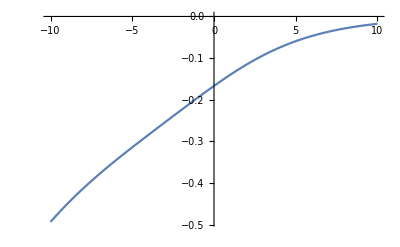

```mathematica
Plot[K[s], {s, -10, 10}]
```

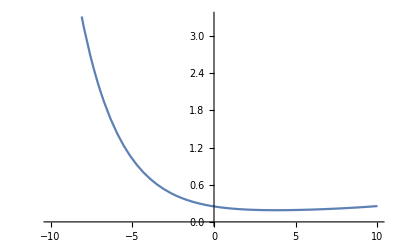

```mathematica
Plot[F[s], {s, -10, 10}]
```

```mathematica
Plot3D[H[s,t], {s, -10, 10}, {t, -10, 10}]
```

-Graphics3D-

```mathematica
Plot3D[T[s,t], {s, -10, 10}, {t, -10, 10}]
```

-Graphics3D-

```mathematica
Plot3D[W[s,t], {s, -10, 10}, {t, -10, 10}]
```

-Graphics3D-

```mathematica
Plot3D[S[s,t], {s, -10, 10}, {t, -10, 10}]
```

-Graphics3D-

### Limit of functions with one variable in ▽ when s→0

```mathematica
commutativeonevariablefunction[11]=Limit[Flog[11],s->0]
```

{{1/3,0,0},{0,1/12,0},{0,0,1/12}}

```mathematica
commutativeonevariablefunction[12]=Limit[Flog[12],s->0]
```

{{0,1/4,0},{1/4,0,0},{0,0,0}}

```mathematica
commutativeonevariablefunction[13]=Limit[Flog[13],s->0]
```

{{0,0,1/4},{0,0,0},{1/4,0,0}}

```mathematica
commutativeonevariablefunction[22]=Limit[Flog[22],s->0]
```

{{1/12,0,0},{0,1/3,0},{0,0,1/12}}

```mathematica
commutativeonevariablefunction[23]=Limit[Flog[23],s->0]
```

{{0,0,0},{0,0,1/4},{0,1/4,0}}

```mathematica
commutativeonevariablefunction[33]=Limit[Flog[33],s->0]
```

{{1/12,0,0},{0,1/12,0},{0,0,1/3}}

```mathematica
CommutativeOnevar=Simplify[commutativeonevariablefunction[11].(Subscript[δ, 1][Subscript[δ, 1][h/2]]*IdentityMatrix[3])+commutativeonevariablefunction[12].(Subscript[δ, 1][Subscript[δ, 2][h/2]]*IdentityMatrix[3])+commutativeonevariablefunction[13].(Subscript[δ, 1][Subscript[δ, 3][h/2]]*IdentityMatrix[3])+commutativeonevariablefunction[22].(Subscript[δ, 2][Subscript[δ, 2][h/2]]*IdentityMatrix[3])+commutativeonevariablefunction[23].(Subscript[δ, 2][Subscript[δ, 3][h/2]]*IdentityMatrix[3])+commutativeonevariablefunction[33].(Subscript[δ, 3][Subscript[δ, 3][h/2]]*IdentityMatrix[3])]
```

{{1/24 (4 δ_1[δ_1[h]]+δ_2[δ_2[h]]+δ_3[δ_3[h]]),1/8 δ_1[δ_2[h]],1/8 δ_1[δ_3[h]]},{1/8 δ_1[δ_2[h]],1/24 (δ_1[δ_1[h]]+4 δ_2[δ_2[h]]+δ_3[δ_3[h]]),1/8 δ_2[δ_3[h]]},{1/8 δ_1[δ_3[h]],1/8 δ_2[δ_3[h]],1/24 (δ_1[δ_1[h]]+δ_2[δ_2[h]]+4 δ_3[δ_3[h]])}}

### Limit of functions with two variables in ▽ when s,t→0

```mathematica
commutativetwovariablefunction[1,1]=Limit[Limit[Flog[1,1],s->0],t->0]
```

{{1/6,0,0},{0,-1/3,0},{0,0,-1/3}}

```mathematica
commutativetwovariablefunction[1,2]=Limit[Limit[Flog[1,2],s->0],t->0]
```

{{0,11/12,0},{-5/12,0,0},{0,0,0}}

```mathematica
commutativetwovariablefunction[1,3]=Limit[Limit[Flog[1,3],s->0],t->0]
```

{{0,0,11/12},{0,0,0},{-5/12,0,0}}

```mathematica
commutativetwovariablefunction[2,1]=Limit[Limit[Flog[2,1],s->0],t->0]
```

{{0,-5/12,0},{11/12,0,0},{0,0,0}}

```mathematica
commutativetwovariablefunction[2,2]=Limit[Limit[Flog[2,2],s->0],t->0]
```

{{-1/3,0,0},{0,1/6,0},{0,0,-1/3}}

```mathematica
commutativetwovariablefunction[2,3]=Limit[Limit[Flog[2,3],s->0],t->0]
```

{{0,0,0},{0,0,11/12},{0,-5/12,0}}

```mathematica
commutativetwovariablefunction[3,1]=Limit[Limit[Flog[3,1],s->0],t->0]
```

{{0,0,-5/12},{0,0,0},{11/12,0,0}}

```mathematica
commutativetwovariablefunction[3,2]=Limit[Limit[Flog[3,2],s->0],t->0]
```

{{0,0,0},{0,0,-5/12},{0,11/12,0}}

```mathematica
commutativetwovariablefunction[3,3]=Limit[Limit[Flog[3,3],s->0],t->0]
```

{{-1/3,0,0},{0,-1/3,0},{0,0,1/6}}

```mathematica
commutativetwovariablefunction[1,1].(Subscript[δ, 1][h/2]*Subscript[δ, 1][h/2]*IdentityMatrix[3])
```

{{1/24 δ_1[h]^2,0,0},{0,-1/12 δ_1[h]^2,0},{0,0,-1/12 δ_1[h]^2}}

```mathematica
CommutativeTwovar=Simplify[Sum[commutativetwovariablefunction[i,j].(Subscript[δ, i][h/2]*Subscript[δ, j][h/2]*IdentityMatrix[3]),{i,1,dim},{j,1,dim}]]
```

{{1/24 (δ_1[h]^2-2 (δ_2[h]^2+δ_3[h]^2)),1/8 δ_1[h] δ_2[h],1/8 δ_1[h] δ_3[h]},{1/8 δ_1[h] δ_2[h],1/24 (-2 δ_1[h]^2+δ_2[h]^2-2 δ_3[h]^2),1/8 δ_2[h] δ_3[h]},{1/8 δ_1[h] δ_3[h],1/8 δ_2[h] δ_3[h],1/24 (-2 δ_1[h]^2-2 δ_2[h]^2+δ_3[h]^2)}}

```mathematica
CommutativeOnevar
```

{{1/24 (4 δ_1[δ_1[h]]+δ_2[δ_2[h]]+δ_3[δ_3[h]]),1/8 δ_1[δ_2[h]],1/8 δ_1[δ_3[h]]},{1/8 δ_1[δ_2[h]],1/24 (δ_1[δ_1[h]]+4 δ_2[δ_2[h]]+δ_3[δ_3[h]]),1/8 δ_2[δ_3[h]]},{1/8 δ_1[δ_3[h]],1/8 δ_2[δ_3[h]],1/24 (δ_1[δ_1[h]]+δ_2[δ_2[h]]+4 δ_3[δ_3[h]])}}

```mathematica
Expand[CommutativeTwovar]
```

{{1/24 δ_1[h]^2-1/12 δ_2[h]^2-1/12 δ_3[h]^2,1/8 δ_1[h] δ_2[h],1/8 δ_1[h] δ_3[h]},{1/8 δ_1[h] δ_2[h],-1/12 δ_1[h]^2+1/24 δ_2[h]^2-1/12 δ_3[h]^2,1/8 δ_2[h] δ_3[h]},{1/8 δ_1[h] δ_3[h],1/8 δ_2[h] δ_3[h],-1/12 δ_1[h]^2-1/12 δ_2[h]^2+1/24 δ_3[h]^2}}

```mathematica
Expand[Simplify[CommutativeOnevar+CommutativeTwovar]]//MatrixForm
```

(1/24 δ_1[h]^2+1/6 δ_1[δ_1[h]]-1/12 δ_2[h]^2+1/24 δ_2[δ_2[h]]-1/12 δ_3[h]^2+1/24 δ_3[δ_3[h]] | 1/8 δ_1[δ_2[h]]+1/8 δ_1[h] δ_2[h] | 1/8 δ_1[δ_3[h]]+1/8 δ_1[h] δ_3[h]
1/8 δ_1[δ_2[h]]+1/8 δ_1[h] δ_2[h] | -1/12 δ_1[h]^2+1/24 δ_1[δ_1[h]]+1/24 δ_2[h]^2+1/6 δ_2[δ_2[h]]-1/12 δ_3[h]^2+1/24 δ_3[δ_3[h]] | 1/8 δ_2[δ_3[h]]+1/8 δ_2[h] δ_3[h]
1/8 δ_1[δ_3[h]]+1/8 δ_1[h] δ_3[h] | 1/8 δ_2[δ_3[h]]+1/8 δ_2[h] δ_3[h] | -1/12 δ_1[h]^2+1/24 δ_1[δ_1[h]]-1/12 δ_2[h]^2+1/24 δ_2[δ_2[h]]+1/24 δ_3[h]^2+1/6 δ_3[δ_3[h]])